# multi-level atom master equation

P. Huft

For solving time dynamics of a density matrix describing an individual multi-level atom, with a Hamiltonian accounting for interaction with multiple classical light fields, and Linblad terms to account for spontaneous emission.

See Mark’s atomic notes, Eqs. 12.18 (the expression for the general density matrix equation matrix elements for N levels and M fields, right before the Optical pumping of Holmium section). Note that the second two sums in the first line of 12.18b should be constrained such that j!=l in the first one and k!=j in the second-- this is because the decay of coherences does not depend on populations. The second sum needs to be split so that the first index of rho is greater than the second. This means that in one of the sums the complex conjugate of the coherence will have to be used since we are dropping redundant coherences rho_{k,j>k}. This last point was addressed in the version of MEqs in setup, but not in the version for debugging with two and four level atoms (the associated errors do not manifest themselves there though).

To-do:
[*] produce optical Bloch eqs with finite upper state lifetime, as a check on the equation generation
[*] Mark’s 4-level example
[*] produce few level eqs for Rb atom
[*] optical pumping of Rb with D1 and D2 line transitions
[] add small B field Zeeman splitting to energies

## setup - run first

```mathematica
constsdir="..\\constants\\";
imagedir=FileNameJoin[{NotebookDirectory[],"\\images\\"}];
AppendTo[$Path, FileNameJoin[{NotebookDirectory[],constsdir}]];
SetDirectory[NotebookDirectory[]];
<<"physconsts.m"
<<"rbconsts.m"
conj[z_]:=z/.{ⅈ-> -ⅈ,-ⅈ->ⅈ};
imag[z_]:=(z-conj[z])/2;
δsym[a_,b_]:=KroneckerDelta[SymbolName[a],SymbolName[b]];
TrueFalse[x_]:=If[x==0,False,True];(*python-like numeric True/False function*)
OoM[x_]:=Floor[Log10[Abs[x]+10^-9]+0.5];
DropHiOsc[detuning_,oom_]:=If[OoM[detuning/(2π)]<oom,1,0](*returns 0 (1) if O[detuning/(2π)] is more (less) than a specified order of magnitude. can by used as a multiplier to drop potentially highly-oscillatory terms*)
OrbAngLetter[L_]:=Switch[L,0,"S",1,"P",2,"D",3,"F"];
KetForm[state_]:=state[[1]] Subscript[OrbAngLetter[state[[2]]], state[[3]]//Rationalize],state[[4]],state[[5]];

(*the double letters denote the upper state quantum numbers*)
E1MatElemHF[{J_,F_,mF_},{JJ_,FF_,mFF_},q_]:=(-1)^(1+i+JJ+F)√(2F+1)SixJSymbol[{J,i,F},{FF,1,JJ}]ClebschGordan[{F,mF},{1,q},{FF,mFF}];
δ[a_,b_]:=KroneckerDelta[a,b];
SetOptions[Plot,Axes->False,Frame->{True,True,False,False},LabelStyle->Directive[Black, 14],ImageSize->Medium];
SetOptions[PolarPlot,PolarAxes->True,PolarGridLines->Automatic,PolarTicks->{Drop[Table[i,{i,0,2 Pi,Pi/4}],-1],Automatic},LabelStyle->Directive[Black, 15],ImageSize->Medium];
(*some units*)
ppm = 10^-6;
GHz=10^9;
MHz=10^6;
(*the population and coherence indices for a ρ vector ordered the same as the equations generated by the MEqs used in the two- and four-level examples*)
Indices[dim_]:=Module[{i=Floor[dim(dim+1)/2+0.5],m=Floor[dim(dim+1)/2+0.5],j=2,pops={},cohs={}},
While[i>0,
AppendTo[pops,i];
i-=j;
j++;
];
{Reverse[pops],Complement[Range[dim(dim+1)/2],pops]}
]
Clear[MEqs]
MEqs[stateList_,fieldAmplitudes_,detunings_,dipoleMatrixElement_,decayRate_,dropFastOoM_,excludeIndices_:{}]:=Module[{drop,states=stateList,Ep=fieldAmplitudes,d=dipoleMatrixElement,γ=decayRate,Δ=detunings,l=1,k=1,dim=1,dimE=1,populationRHS, coherenceRHS,populationDriving,populationDecay,coherenceDriving,coherenceDecay,RHS=0,Eqs={},HO,Ex},
(*Builds the density matrix master equation in Linblad form for each element Subscript[ρ, k,l] with k>l and k increasing in order of energy. The coherence terms are actually ρ̃=ρⅇ^-ⅈωt.

--- Params ---
fieldAmplitudes, detunings, dipoleMatrixElement, and decayRate: functions that depend on state indices j,k and field indices p to return the appropriate quantity. See usage below.

dropFastOoM: an order of magnitude of the detuning (in the chosen energy units of the states and fields, e.g. GHz).

excludeIndices: a list of indices {k,l} for which equations for Subscript[ρ, k,l] and dependence on Subscript[ρ, k,l] in other eqs will be dropped
*)
dim = Length[states];
dimE=Length[Ep];
(*--multipliers for systematically dropping terms--*)
Table[Subscript[HO, p,i,j]=DropHiOsc[Δ[p,i,j],dropFastOoM],{p,Range[dimE]},{i,Range[dim]},{j,Range[dim]}];(*for removing highly oscillatory (far off-resonant) terms*)
Table[Subscript[Ex, k,l]=Subscript[Ex, l,k]=Boole[!MemberQ[excludeIndices,{k,l}]],{l,Range[dim]},{k,Range[l,dim]}];(*for removing the equations for and terms with Subscript[ρ, k,l] if {k,l} ∈ excludeIndices*)

(*--Generate the population eqs--*)
For[k=1,k<dim+1,k++,
RHS=
-Sum[γ[j,k]Subscript[ρ, k,k][t],{j,Range[1,k-1]}]+Sum[γ[k,j]Subscript[ρ, j,j][t],{j,Range[k+1,dim]}]
-ⅈ/(2ℏ)(Sum[(-Ep[[p]]d[k,j,p]Subscript[ρ, k,j][t]*Exp[-ⅈ Δ[p,k,j]t]+Ep[[p]]*d[j,k,p]Subscript[ρ, k,j][t]Exp[ⅈ Δ[p,k,j]t])Subscript[HO, p,k,j] Subscript[Ex, k,j],{p,Range[dimE]},{j,Range[1,k-1]}]
+Sum[(Ep[[p]]d[j,k,p]Subscript[ρ, j,k][t]*Exp[-ⅈ Δ[p,j,k]t]-Ep[[p]]*d[k,j,p]Subscript[ρ, j,k][t]Exp[ⅈ Δ[p,j,k]t])Subscript[HO, p,j,k] Subscript[Ex, j,k],{p,Range[dimE]},{j,Range[k+1,dim]}]);
AppendTo[Eqs,D[Subscript[ρ, k,k][t],t]==RHS];
];
(*--Generate the coherence eqs--*)
For[l=1,l<dim+1,l++,
For[k=l+1,k<dim+1,k++,
If[!MemberQ[excludeIndices,{k,l}],
RHS=1/2(-(Sum[γ[j,k],{j,Range[1,k-1]}]+Sum[γ[j,l],{j,Range[1,l-1]}])Subscript[ρ, k,l][t]
+Sum[γ[k,j]Subscript[ρ, j,l][t](1-δ[j,l])Subscript[Ex, j,l],{j,Range[k+1,dim]}]+Sum[γ[l,j]Subscript[ρ, k,j][t](1-δ[k,j])Subscript[Ex, k,j],{j,Range[l+1,k-1]}]+Sum[γ[l,j]Subscript[ρ, j,k][t]*(1-δ[k,j])Subscript[Ex, j,k],{j,Range[k+1,dim]}]
-ⅈ/ℏ(Sum[-Ep[[p]]d[k,j,p]Subscript[ρ, l,j][t]*Exp[-ⅈ Δ[p,k,j]t] Subscript[HO, p,k,j] Subscript[Ex, l,j]+Ep[[p]]*d[j,l,p]Subscript[ρ, k,j][t]Exp[ⅈ Δ[p,l,j]t] Subscript[HO, p,l,j] Subscript[Ex, k,j],{p,Range[dimE]},{j,Range[1,l-1]}]
+Sum[Ep[[p]](d[j,l,p]Subscript[ρ, k,j][t]Exp[-ⅈ Δ[p,j,l]t] Subscript[HO, p,j,l] Subscript[Ex, k,j]-d[k,j,p]Subscript[ρ, j,l][t]Exp[-ⅈ Δ[p,k,j]t] Subscript[HO, p,k,j] Subscript[Ex, j,l]),{p,Range[dimE]},{j,Range[l,k-1]}]
+Sum[Ep[[p]]d[j,l,p]Subscript[ρ, j,k][t]*Exp[-ⅈ Δ[p,j,l]t] Subscript[HO, p,j,l] Subscript[Ex, j,k]-Ep[[p]]*d[k,j,p]Subscript[ρ, j,l][t]Exp[ⅈ Δ[p,j,k]t] Subscript[HO, p,j,k] Subscript[Ex, j,l],{p,Range[dimE]},{j,Range[k,dim]}]));
AppendTo[Eqs,D[Subscript[ρ, k,l][t],t]==RHS];
];
];
];

Eqs
]
```

## Two-level algebra

The standard two-level density matrix equation w/o decoherence. Eq 10.26 in Mark’s notes.

```mathematica
Clear[ρ,d,ef]
ρm=Array[Subscript[ρ, #1,#2][t]&,{2,2}];
ef=Ε;
H =-ef({{0, d*}, {d, ωa}});
eqs=ⅈ (ρm.H - H.ρm);
Flatten[eqs][[{1,3,4}]]//FullSimplify//TableForm//TraditionalForm
```

-ⅈ Ε (d ρ_(1,2)(t)-Conjugate[d] ρ_(2,1)(t))
ⅈ Ε (d ρ_(1,1)(t)-d ρ_(2,2)(t)+ωa ρ_(2,1)(t))
ⅈ Ε (d ρ_(1,2)(t)-Conjugate[d] ρ_(2,1)(t))

Expressing the  field in terms of its CW and ACW rotating parts, and using the tilde ρ for the coherence, we have eq. 10.28 from Mark’s notes (up to incoherence terms)

```mathematica
Clear[ρ,d,ef]
ρm=Array[Subscript[ρ, #1,#2][t] ⅇ^(Sign[#2-#1] ⅈ ω t)&,{2,2}];(*the Sign[] converts Subscript[ρ, eg] to OverTilde[Subscript[ρ, eg]]=OverTilde[Subscript[ρ, eg]] ⅇ^-ⅈωt*)
ef=Ε/2 ⅇ^(-ⅈ ω t)+(Ε*)/2 ⅇ^(ⅈ ω t);
H =-ef({{0, d*}, {d, ωa}});
eqs=Flatten[ⅈ (ρm.H - H.ρm)];
eqs[[3]]-=ⅈ ω Subscript[ρ, 2,1];(*this and the next line finish the ρ tilde sub*)
eqs[[3]]*=ⅇ^(-ⅈ ω t);
eqs[[{1,3,4}]]//Together//TableForm//TraditionalForm
```

-1/2 ⅈ ⅇ^(-2 ⅈ t ω) (Ε+Conjugate[Ε] ⅇ^(2 ⅈ t ω)) (-Conjugate[d] ρ_(2,1)(t)+d ⅇ^(2 ⅈ t ω) ρ_(1,2)(t))
1/2 ⅈ ⅇ^(-3 ⅈ t ω) (d Conjugate[Ε] ⅇ^(3 ⅈ t ω) ρ_(1,1)(t)-d Conjugate[Ε] ⅇ^(3 ⅈ t ω) ρ_(2,2)(t)+ωa Conjugate[Ε] ⅇ^(2 ⅈ t ω) ρ_(2,1)(t)+d Ε ⅇ^(ⅈ t ω) ρ_(1,1)(t)-d Ε ⅇ^(ⅈ t ω) ρ_(2,2)(t)+Ε ωa ρ_(2,1)(t)-2 ω ρ_(2,1) ⅇ^(2 ⅈ t ω))
1/2 ⅈ ⅇ^(-2 ⅈ t ω) (Ε+Conjugate[Ε] ⅇ^(2 ⅈ t ω)) (-Conjugate[d] ρ_(2,1)(t)+d ⅇ^(2 ⅈ t ω) ρ_(1,2)(t))

## Two-level atom, low-level test for debugging

First, leave everything symbolic to see if the correct equation is generated (check with eq. 10.28 of Mark’s notes). For this symbolic test I have set ℏ=1 below. 

Upon inspection there are some differences, particularly in the coherence equation. I think this is because the equation below does not make the ρ̃ substitution.

```mathematica
(*group states by {quantum numbers,ω}, ascending in energy*)
Clear[t]
(*simplifies debugging*)
states={{gg,0},{ee,ωa}};
{level,energies}=Transpose@states;
(*lists of field amplitudes and ang. freq*)
Efields={{E1,ω}};
{Ep,ωp} = Transpose@Efields;
dimE=Length[Ep];
(*things that depend on a pair of state indices j and k:*)
d[j_,k_]:=(1-δ[j,k])If[k<j,deg ,dge];(*trivial*)
γ[j_,k_]:= (1-δ[j,k])γeg;
Δ[p_,k_,j_]:=ωp[[p]]-(energies[[k]]-energies[[j]]);
(*trivial, 2 is upper state*)
(*build the equations for each element of the density matrix.
redundant equations,i.e. complex conjugates of the off-diagonals are omitted.*)
dim = Length[states];
Eqs={};
For[l=1,l<dim+1,l++,
For[k=l,k<dim+1,k++,
RHS=
δ[k,l](-Sum[γ[j,k]Subscript[ρ, k,k][t],{j,Range[1,k-1]}]+Sum[γ[k,j]Subscript[ρ, j,j][t],{j,Range[k+1,dim]}]
-(ⅈ/2)(Sum[-Ep[[p]]d[k,j]Subscript[ρ, k,j][t]*Exp[-ⅈ Δ[p,k,j]t]+Ep[[p]]*d[j,k]Subscript[ρ, k,j][t]Exp[ⅈ Δ[p,k,j]t],{p,Range[dimE]},{j,Range[1,k-1]}]
+Sum[Ep[[p]]d[j,k]Subscript[ρ, j,k][t]*Exp[-ⅈ Δ[p,j,k]t]-Ep[[p]]*d[k,j]Subscript[ρ, j,k][t]Exp[ⅈ Δ[p,j,k]t],{p,Range[dimE]},{j,Range[k+1,dim]}]))
+(1/2)(1-δ[k,l])(-(Sum[γ[j,k],{j,Range[1,k-1]}]+Sum[γ[j,l],{j,Range[1,l-1]}])Subscript[ρ, k,l][t]
+Sum[γ[k,j]Subscript[ρ, j,l][t]δ[j,l],{j,Range[k+1,dim]}]+Sum[γ[l,j]Subscript[ρ, k,j][t]δ[j,l],{j,Range[l+1,dim]}]
-ⅈ(Sum[-Ep[[p]]d[k,j]Subscript[ρ, l,j][t]*Exp[-ⅈ Δ[p,k,j]t]+Ep[[p]]*d[j,l]Subscript[ρ, k,j][t]Exp[ⅈ Δ[p,l,j]t],{p,Range[dimE]},{j,Range[1,l-1]}]
+Sum[Ep[[p]](d[j,l]Subscript[ρ, k,j][t]Exp[-ⅈ Δ[p,j,l]t]-d[k,j]Subscript[ρ, j,l][t]Exp[-ⅈ Δ[p,k,j]t]),{p,Range[dimE]},{j,Range[l,k-1]}]
+Sum[Ep[[p]]d[j,l]Subscript[ρ, j,k][t]*Exp[-ⅈ Δ[p,j,l]t]-Ep[[p]]*d[k,j]Subscript[ρ, j,l][t]Exp[ⅈ Δ[p,j,k]t],{p,Range[dimE]},{j,Range[k,dim]}]))//FullSimplify;
AppendTo[Eqs,D[Subscript[ρ, k,l][t],t]==RHS];
Print[TraditionalForm[D[Subscript[ρ, k,l][t],t]==RHS//TrigToExp]];
]
]
```

ρ_(1,1)'(t)==-1/2 ⅈ deg E1 ⅇ^(-ⅈ t (ω-ωa)) Conjugate[ρ_(2,1)(t)]+1/2 ⅈ dge Conjugate[E1] ρ_(2,1)(t) ⅇ^(ⅈ t (ω-ωa))+γeg ρ_(2,2)(t)

ρ_(2,1)'(t)==-1/2 ⅈ deg E1 ⅇ^(-ⅈ t (ω-ωa)) Conjugate[ρ_(2,2)(t)]+1/2 ⅈ deg E1 ρ_(1,1)(t) ⅇ^(-ⅈ t (ω-ωa))-1/2 γeg ρ_(2,1)(t)

ρ_(2,2)'(t)==1/2 ⅈ deg E1 ⅇ^(-ⅈ t (ω-ωa)) Conjugate[ρ_(2,1)(t)]-1/2 ⅈ dge Conjugate[E1] ρ_(2,1)(t) ⅇ^(ⅈ t (ω-ωa))-γeg ρ_(2,2)(t)

Test of simulated Rabi oscillations and relaxation.

```mathematica
states={{gg,0},{ee,1}};
{level,energies}=Transpose@states;
(*lists of field amplitudes and ang. freq*)
Efields={{1,1}};
{Ep,ωp} = Transpose@Efields;
dimE=Length[Ep];
(*things that depend on a pair of state indices j and k:*)
d[j_,k_]:=(1-δ[j,k]);(*trivial*)
γ[j_,k_]:=(1-δ[j,k])0.1;
Δ[p_,k_,j_]:=ωp[[p]]-(energies[[k]]-energies[[j]]);
Clear[Eqs];
Eqs={};
For[l=1,l<dim+1,l++,
For[k=l,k<dim+1,k++,
RHS=
δ[k,l](-Sum[γ[j,k]Subscript[ρ, k,k][t],{j,Range[1,k-1]}]+Sum[γ[k,j]Subscript[ρ, j,j][t],{j,Range[k+1,dim]}]
-ⅈ/2(Sum[-Ep[[p]]d[k,j]Subscript[ρ, k,j][t]*Exp[-ⅈ Δ[p,k,j]t]+Ep[[p]]*d[j,k]Subscript[ρ, k,j][t]Exp[ⅈ Δ[p,k,j]t],{p,Range[dimE]},{j,Range[1,k-1]}]
+Sum[Ep[[p]]d[j,k]Subscript[ρ, j,k][t]*Exp[-ⅈ Δ[p,j,k]t]-Ep[[p]]*d[k,j]Subscript[ρ, j,k][t]Exp[ⅈ Δ[p,j,k]t],{p,Range[dimE]},{j,Range[k+1,dim]}]))
+1/2(1-δ[k,l])(-(Sum[γ[j,k],{j,Range[1,k-1]}]+Sum[γ[j,l],{j,Range[1,l-1]}])Subscript[ρ, k,l][t]
+Sum[γ[k,j]Subscript[ρ, j,l][t]δ[j,l],{j,Range[k+1,dim]}]+Sum[γ[l,j]Subscript[ρ, k,j][t]δ[j,l],{j,Range[l+1,dim]}]
-ⅈ(Sum[-Ep[[p]]d[k,j]Subscript[ρ, l,j][t]*Exp[-ⅈ Δ[p,k,j]t]+Ep[[p]]*d[j,l]Subscript[ρ, k,j][t]Exp[ⅈ Δ[p,l,j]t],{p,Range[dimE]},{j,Range[1,l-1]}]
+Sum[Ep[[p]](d[j,l]Subscript[ρ, k,j][t]Exp[-ⅈ Δ[p,j,l]t]-d[k,j]Subscript[ρ, j,l][t]Exp[-ⅈ Δ[p,k,j]t]),{p,Range[dimE]},{j,Range[l,k-1]}]
+Sum[Ep[[p]]d[j,l]Subscript[ρ, j,k][t]*Exp[-ⅈ Δ[p,j,l]t]-Ep[[p]]*d[k,j]Subscript[ρ, j,l][t]Exp[ⅈ Δ[p,j,k]t],{p,Range[dimE]},{j,Range[k,dim]}]))//FullSimplify;
AppendTo[Eqs,D[Subscript[ρ, k,l][t],t]==RHS];
Print[TraditionalForm[D[Subscript[ρ, k,l][t],t]==RHS]];
]
]
tmax=10/(Ep[[1]]d[1,2]);
rho={Subscript[ρ, 1,1][t],Subscript[ρ, 2,1][t],Subscript[ρ, 2,2][t]};
rho0={1,0,0};
icEqs=Array[(rho/.t-> 0)[[#]]==rho0[[#]]&,Length[rho]];
{time,soln}= Timing[First@NDSolve[Flatten@Join[Eqs,icEqs], rho, {t,0,tmax}]];
Print["Time to run sim: ",time];
```

ρ_(1,1)'(t)==-ⅈ Re(ρ_(2,1)(t))+ⅈ ρ_(2,1)(t)+0.1 ρ_(2,2)(t)

ρ_(2,1)'(t)==(0.-0.5 ⅈ) Conjugate[ρ_(2,2)(t)]+(0.+0.5 ⅈ) ρ_(1,1)(t)-0.05 ρ_(2,1)(t)

ρ_(2,2)'(t)==-0.1 ρ_(2,2)(t)+ⅈ (Re(ρ_(2,1)(t))-ρ_(2,1)(t))

Time to run sim: 0.

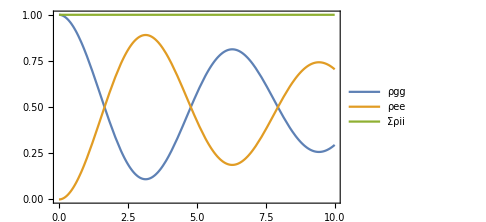

```mathematica
plt ={};
labels={"ρgg","ρee","Σρii"};
For[i=1, i<Length[soln]+1,i++,
AppendTo[plt,soln[[i,2]]]
];
populations={1,3};
AppendTo[plt,Total[soln[[populations,2]]]];
AppendTo[populations,-1];
Plot[Evaluate[plt[[populations]]], {t, 0, tmax},PlotRange->All,PlotLegends->labels]
```

## Two level atom, high-level test

Convert diff eqs to a module for easier deployment. The list of states, the list of fields, and factors which depend on two states j and k, such as the dipole matrix element, will be passed into a module that generates the equations, so that the module can be left completely general and defined only once at the top of this notebook.

```mathematica
Clear[MEqs]
MEqs[stateList_,fieldAmplitudes_,detunings_,dipoleMatrixElement_,decayRate_]:=Module[{states=stateList,Ep=fieldAmplitudes,d=dipoleMatrixElement,γ=decayRate,Δ=detunings,l=1,k=1,dim=1,dimE=1,RHS=0,Eqs={}},
(*Builds the density matrix master equation in Linblad form for each element Subscript[ρ, k,l] with k>l and k increasing in order of energy. The coherence terms are actually ρ̃=ρⅇ^-ⅈωt.*)
dim = Length[states];
dimE=Length[Ep];
For[l=1,l<dim+1,l++,
For[k=l,k<dim+1,k++,
RHS=
δ[k,l](-Sum[γ[j,k]Subscript[ρ, k,k][t],{j,Range[1,k-1]}]+Sum[γ[k,j]Subscript[ρ, j,j][t],{j,Range[k+1,dim]}]
-ⅈ/2(Sum[-Ep[[p]]d[k,j]Subscript[ρ, k,j][t]*Exp[-ⅈ Δ[p,k,j]t]+Ep[[p]]*d[j,k]Subscript[ρ, k,j][t]Exp[ⅈ Δ[p,k,j]t],{p,Range[dimE]},{j,Range[1,k-1]}]
+Sum[Ep[[p]]d[j,k]Subscript[ρ, j,k][t]*Exp[-ⅈ Δ[p,j,k]t]-Ep[[p]]*d[k,j]Subscript[ρ, j,k][t]Exp[ⅈ Δ[p,j,k]t],{p,Range[dimE]},{j,Range[k+1,dim]}]))
+1/2(1-δ[k,l])(-(Sum[γ[j,k],{j,Range[1,k-1]}]+Sum[γ[j,l],{j,Range[1,l-1]}])Subscript[ρ, k,l][t]
+Sum[γ[k,j]Subscript[ρ, j,l][t]δ[j,l],{j,Range[k+1,dim]}]+Sum[γ[l,j]Subscript[ρ, k,j][t]δ[j,l],{j,Range[l+1,dim]}]
-ⅈ(Sum[-Ep[[p]]d[k,j]Subscript[ρ, l,j][t]*Exp[-ⅈ Δ[p,k,j]t]+Ep[[p]]*d[j,l]Subscript[ρ, k,j][t]Exp[ⅈ Δ[p,l,j]t],{p,Range[dimE]},{j,Range[1,l-1]}]
+Sum[Ep[[p]](d[j,l]Subscript[ρ, k,j][t]Exp[-ⅈ Δ[p,j,l]t]-d[k,j]Subscript[ρ, j,l][t]Exp[-ⅈ Δ[p,k,j]t]),{p,Range[dimE]},{j,Range[l,k-1]}]
+Sum[Ep[[p]]d[j,l]Subscript[ρ, j,k][t]*Exp[-ⅈ Δ[p,j,l]t]-Ep[[p]]*d[k,j]Subscript[ρ, j,l][t]Exp[ⅈ Δ[p,j,k]t],{p,Range[dimE]},{j,Range[k,dim]}]))//FullSimplify;
AppendTo[Eqs,D[Subscript[ρ, k,l][t],t]==RHS];
(*Print[TraditionalForm[D[Subscript[ρ, k,l][t],t]==RHS]];*)
(*todo: subtract off the highly oscillatory terms*)
];
];
Eqs
]
```

```mathematica
states={{gg,0},{ee,1}};
{level,energies}=Transpose@states;
(*lists of field amplitudes and ang. freq*)
Efields={{1,1}};
{Ep,ωp} = Transpose@Efields;
dimE=Length[Ep];
(*things that depend on a pair of state indices j and k:*)
d[j_,k_]:=(1-δ[j,k]);(*trivial*)
γ[j_,k_]:=(1-δ[j,k])0.1;
Δ[p_,k_,j_]:=ωp[[p]]-(energies[[k]]-energies[[j]]);
Eqs = MEqs[states,Ep,Δ,d,γ];
tmax=10/(Ep[[1]]d[1,2]);
rho={Subscript[ρ, 1,1][t],Subscript[ρ, 2,1][t],Subscript[ρ, 2,2][t]};
rho0={1,0,0};
icEqs=Array[(rho/.t-> 0)[[#]]==rho0[[#]]&,Length[rho]];
{time,soln}= Timing[First@NDSolve[Flatten@Join[Eqs,icEqs], rho, {t,0,tmax}]];
Print["Time to run sim: ",time];
plt ={};
labels={"ρgg","ρee","Σρii"};
For[i=1, i<Length[soln]+1,i++,
AppendTo[plt,soln[[i,2]]]
];
populations={1,3};
AppendTo[plt,Total[soln[[populations,2]]]];
AppendTo[populations,-1];
Plot[Evaluate[plt[[populations]]], {t, 0, tmax},PlotRange->All,PlotLegends->labels]
```

Time to run sim: 0.

-Graphics-

## Four level atom, high-level test

Reproduce the four level evolution shown in Mark’s notes figured 12.7. I have not made the rotating wave  approximation, and in order to ensure that the fields only couple neighboring levels, I make the energy differences very different between each pair of levels. I redefine MEqs below with additional factors so that rapidly oscillating terms are set to zero. This is done by checking whether the detuning in an exponential is on the order of the transition considered.

```mathematica
Clear[MEqs]
MEqs[stateList_,fieldAmplitudes_,detunings_,dipoleMatrixElement_,decayRate_,dropFastOOM_]:=Module[{drop,states=stateList,Ep=fieldAmplitudes,d=dipoleMatrixElement,γ=decayRate,Δ=detunings,l=1,k=1,dim=1,dimE=1,RHS=0,Eqs={}},
(*Builds the density matrix master equation in Linblad form for each element Subscript[ρ, k,l] with k>l and k increasing in order of energy. The coherence terms are actually ρ̃=ρⅇ^-ⅈωt.*)
dim = Length[states];
dimE=Length[Ep];
drop[δ_]:=DropHiOsc[δ,dropFastOOM];
For[l=1,l<dim+1,l++,
For[k=l,k<dim+1,k++,
RHS=
δ[k,l](-Sum[γ[j,k]Subscript[ρ, k,k][t],{j,Range[1,k-1]}]+Sum[γ[k,j]Subscript[ρ, j,j][t],{j,Range[k+1,dim]}]
-ⅈ/(2ℏ)(Sum[-Ep[[p]]d[k,j,p]Subscript[ρ, k,j][t]*Exp[-ⅈ Δ[p,k,j]t]drop[Δ[p,k,j]]+Ep[[p]]*d[j,k,p]Subscript[ρ, k,j][t]Exp[ⅈ Δ[p,k,j]t]drop[Δ[p,k,j]],{p,Range[dimE]},{j,Range[1,k-1]}]
+Sum[Ep[[p]]d[j,k,p]Subscript[ρ, j,k][t]*Exp[-ⅈ Δ[p,j,k]t]drop[Δ[p,j,k]]-Ep[[p]]*d[k,j,p]Subscript[ρ, j,k][t]Exp[ⅈ Δ[p,j,k]t]drop[Δ[p,j,k]],{p,Range[dimE]},{j,Range[k+1,dim]}]))
+1/2(1-δ[k,l])(-(Sum[γ[j,k],{j,Range[1,k-1]}]+Sum[γ[j,l],{j,Range[1,l-1]}])Subscript[ρ, k,l][t]
+Sum[γ[k,j]Subscript[ρ, j,l][t]δ[j,l],{j,Range[k+1,dim]}]+Sum[γ[l,j]Subscript[ρ, k,j][t]δ[j,l],{j,Range[l+1,dim]}]
-ⅈ/ℏ(Sum[-Ep[[p]]d[k,j,p]Subscript[ρ, l,j][t]*Exp[-ⅈ Δ[p,k,j]t]drop[Δ[p,k,j]]+Ep[[p]]*d[j,l,p]Subscript[ρ, k,j][t]Exp[ⅈ Δ[p,l,j]t]drop[Δ[p,l,j]],{p,Range[dimE]},{j,Range[1,l-1]}]
+Sum[Ep[[p]](d[j,l,p]Subscript[ρ, k,j][t]Exp[-ⅈ Δ[p,j,l]t]drop[Δ[p,j,l]]-d[k,j,p]Subscript[ρ, j,l][t]Exp[-ⅈ Δ[p,k,j]t]drop[Δ[p,k,j]]),{p,Range[dimE]},{j,Range[l,k-1]}]
+Sum[Ep[[p]]d[j,l,p]Subscript[ρ, j,k][t]*Exp[-ⅈ Δ[p,j,l]t]drop[Δ[p,j,l]]-Ep[[p]]*d[k,j,p]Subscript[ρ, j,l][t]Exp[ⅈ Δ[p,j,k]t]drop[Δ[p,j,k]],{p,Range[dimE]},{j,Range[k,dim]}]))//FullSimplify;
AppendTo[Eqs,D[Subscript[ρ, k,l][t],t]==RHS];
(*Print[TraditionalForm[D[Subscript[ρ, k,l][t],t]==RHS]];*)
(*todo: subtract off the highly oscillatory terms*)
];
];
Eqs
]
```

```mathematica
(*state labels and energies in arb. units*)
states={{"1",0},{"2",100},{"3",150},{"4",400}};
{level,energies}=Transpose@states;
dim=Length[energies];
(*lists of field amplitudes and ang. freq*)
Clear[Ω1,Ω2,Ω3];
Efields={{ℏ Ω1,100.5},{ℏ Ω2,50.6},{ℏ Ω3,250.1}};
{Ep,ωp} = Transpose@Efields;
dimE=Length[Ep];
(*things that depend on a pair of state indices j and k:*)
d[j_,k_,p_]:=(1-δ[j,k]);(*trivial*)
γ[j_,k_]:=(1-δ[j,k])0;
Δ[p_,k_,j_]:=ωp[[p]]-(energies[[k]]-energies[[j]]);
drop=1; (*terms with detunings of greater order of magnitude than this will be dropped*)
Eqs = MEqs[states,Ep,Δ,d,γ,drop];(*generate the differential equations*)
For[i=1,i<Length[Eqs]+1,i++,
Print[Eqs[[i]]//Expand//TraditionalForm]
]
```

ρ_(1,1)'(t)==(0.+0.5 ⅈ) ⅇ^((0.+0.5 ⅈ) t) Conjugate[Ω1] ρ_(2,1)(t)-(0.+0.5 ⅈ) Ω1 ⅇ^((0.-0.5 ⅈ) t) Conjugate[ρ_(2,1)(t)]

ρ_(2,1)'(t)==(0.-0.5 ⅈ) Ω1 ⅇ^((0.-0.5 ⅈ) t) Conjugate[ρ_(2,2)(t)]+(0.+0.5 ⅈ) ⅇ^((0.+0.6 ⅈ) t) Conjugate[Ω2] ρ_(3,1)(t)+(0.+0.5 ⅈ) Ω1 ⅇ^((0.-0.5 ⅈ) t) ρ_(1,1)(t)

ρ_(3,1)'(t)==(0.+0.5 ⅈ) ⅇ^((0.+0.1 ⅈ) t) Conjugate[Ω3] ρ_(4,1)(t)-(0.+0.5 ⅈ) Ω1 ⅇ^((0.-0.5 ⅈ) t) ρ_(3,2)(t)+(0.+0.5 ⅈ) Ω2 ⅇ^((0.-0.6 ⅈ) t) ρ_(2,1)(t)

ρ_(4,1)'(t)==(0.+0.5 ⅈ) Ω3 ⅇ^((0.-0.1 ⅈ) t) ρ_(3,1)(t)-(0.+0.5 ⅈ) Ω1 ⅇ^((0.-0.5 ⅈ) t) ρ_(4,2)(t)

ρ_(2,2)'(t)==(0.+0.5 ⅈ) Ω1 ⅇ^((0.-0.5 ⅈ) t) Conjugate[ρ_(2,1)(t)]-(0.+0.5 ⅈ) ⅇ^((0.+0.5 ⅈ) t) Conjugate[Ω1] ρ_(2,1)(t)-(0.+0.5 ⅈ) Ω2 ⅇ^((0.-0.6 ⅈ) t) Conjugate[ρ_(3,2)(t)]+(0.+0.5 ⅈ) ⅇ^((0.+0.6 ⅈ) t) Conjugate[Ω2] ρ_(3,2)(t)

ρ_(3,2)'(t)==-(0.+0.5 ⅈ) ⅇ^((0.+0.5 ⅈ) t) Conjugate[Ω1] ρ_(3,1)(t)+(0.-0.5 ⅈ) Ω2 ⅇ^((0.-0.6 ⅈ) t) Conjugate[ρ_(3,3)(t)]+(0.+0.5 ⅈ) ⅇ^((0.+0.1 ⅈ) t) Conjugate[Ω3] ρ_(4,2)(t)+(0.+0.5 ⅈ) Ω2 ⅇ^((0.-0.6 ⅈ) t) ρ_(2,2)(t)

ρ_(4,2)'(t)==-(0.+0.5 ⅈ) ⅇ^((0.+0.5 ⅈ) t) Conjugate[Ω1] ρ_(4,1)(t)-(0.+0.5 ⅈ) Ω2 ⅇ^((0.-0.6 ⅈ) t) ρ_(4,3)(t)+(0.+0.5 ⅈ) Ω3 ⅇ^((0.-0.1 ⅈ) t) ρ_(3,2)(t)

ρ_(3,3)'(t)==(0.+0.5 ⅈ) Ω2 ⅇ^((0.-0.6 ⅈ) t) Conjugate[ρ_(3,2)(t)]-(0.+0.5 ⅈ) ⅇ^((0.+0.6 ⅈ) t) Conjugate[Ω2] ρ_(3,2)(t)-(0.+0.5 ⅈ) Ω3 ⅇ^((0.-0.1 ⅈ) t) Conjugate[ρ_(4,3)(t)]+(0.+0.5 ⅈ) ⅇ^((0.+0.1 ⅈ) t) Conjugate[Ω3] ρ_(4,3)(t)

ρ_(4,3)'(t)==-(0.+0.5 ⅈ) ⅇ^((0.+0.6 ⅈ) t) Conjugate[Ω2] ρ_(4,2)(t)+(0.-0.5 ⅈ) Ω3 ⅇ^((0.-0.1 ⅈ) t) Conjugate[ρ_(4,4)(t)]+(0.+0.5 ⅈ) Ω3 ⅇ^((0.-0.1 ⅈ) t) ρ_(3,3)(t)

ρ_(4,4)'(t)==(0.+0.5 ⅈ) Ω3 ⅇ^((0.-0.1 ⅈ) t) Conjugate[ρ_(4,3)(t)]-(0.+0.5 ⅈ) ⅇ^((0.+0.1 ⅈ) t) Conjugate[Ω3] ρ_(4,3)(t)

Time to run sim: 0.015625

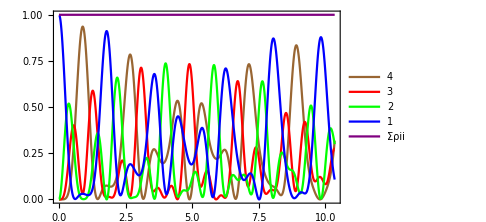

```mathematica
Ω1=Ω2=Ω3=2π;
tmax=65ℏ/(Ep[[1]]d[1,2,1]);
rho=Flatten@Table[Subscript[ρ, k,l][t],{l,1,dim},{k,l,dim}];
rho0=Array[0&,dim(dim+1)/2];
rho0[[1]]=1;
icEqs=Array[(rho/.t-> 0)[[#]]==rho0[[#]]&,Length[rho]];
{time,soln}= Timing[First@NDSolve[Flatten@Join[Eqs,icEqs], rho, {t,0,tmax},Method->Automatic,MaxStepFraction->0.001]];
Print["Time to run sim: ",time];
plt ={};
labels={"4","3","2","1","Σρii"};
For[i=1, i<Length[soln]+1,i++,
AppendTo[plt,soln[[i,2]]]
];
{populations,coherences}=Indices[dim];
AppendTo[plt,Total[soln[[populations,2]]]];
AppendTo[populations,-1];
Plot[Evaluate[plt[[populations]]], {t, 0, tmax},PlotRange->All,PlotLegends->labels,PlotStyle->{Brown, Red,Green, Blue,Purple}]
```

## “Realistic” atom with hyperfine states

Run the 4-level cell above define the equation generator module, MEqs. Now that we are dealing with “realistic” atoms we need to choose some useful units of energy. I use GHz.
Examples to try with a Rb atom in a constrained space to make the test easy to debug:
[] Driving Rabi oscillations between 5S1/2 F=1 and 5P3/2 F=0 states with one field whose linear polarization is angled to equalize the three transition rates.
[] Raman on D2 line on a pair of transitions 5S1/2,F=1,m=1,5S1/2,F=2,m=2 to  5P3/2,F=2,m=2 with linear light quasi-resonant from F=2->F=2 and RH light quasi-resonant on F=1->F=2.  Include the 5S1/2,F=2,m=1 state to which population will eventually end up.

## ^87 Rb - lambda-scheme Raman without spontaneous decay

These eqs are very stiff for large detuning... the population in ρ33 should be essentially zero in this case so the stiffness may be related to Mathematica running into numerical precision issues or not being able to control the step size.

```mathematica
(*states with n,L,J,F,mF, and angular frequency (energy) in 2π*GHz wrt ground state C.o.M. energy*)
ω5sOneHalfF2=2π*2.563005979089;
ω5sOneHalfF1=2π*-4.27167663181519;
ωD2=2π*384230.4844685;
ω5pThreeHalvesF0 =ωD2-2π*.3020738;
ω5pThreeHalvesF2=ωD2-2π*.072911332;
states={{5,0,1/2,1,1,ω5sOneHalfF1},{5,0,1/2,2,2,ω5sOneHalfF2},{5,1,3/2,2,2,ω5pThreeHalvesF2}};
{n,L,J,F,mF,ω}=Transpose@states;
dim=Length[states];

(*list of ground state hyperfine levels F*)
Fglist={1,2};

(*lists of field amplitudes, ang. frequencies, polarization, and angle in rad*)
Clear[Ε1,Ε2,γD1,γD2,dD1,dD2](*leave symbolic so it's easy to read the equations*);
det =2π*1;(*detuning. must be finite, but can be arbitrarily small... where does the 1/0 come from?*)
Efields={{Ε1,ω5pThreeHalvesF2-ω5sOneHalfF1-det,1,0},{Ε2,ω5pThreeHalvesF2-ω5sOneHalfF2-det, 0,0}};
{Ep,ωp,q,θ}=Transpose@Efields;
dimE=Length[Ep];

(*--things that depend on a pair of state indices j and k--*)
E1FineReduced[j_,k_]:=Switch[Sort[{{n[[j]],L[[j]],J[[j]]},{n[[k]],L[[k]],J[[k]]}}],{{5,0,1/2},{5,1,1/2}},dD1,{{5,0,1/2},{5,1,3/2}},dD2,_,0];(*get hardcoded D1 or D2 line reduced dipole matrix element.*)

d[m_,n_,p_]:=Module[{j,k},
{j,k}=Sort[{m,n}];(*because the matrix element is real, it is equal to its complex conjugate. Hence, when the state labels are reversed the value return is the same.*)
Quiet[(-1)^(1+INuc+J[[k]]+F[[j]])√(2F[[j]]+1)SixJSymbol[{J[[j]],INuc,F[[j]]},{F[[k]],1,J[[k]]}]ClebschGordan[{F[[j]],mF[[j]]},{1,q[[p]]},{F[[k]],mF[[k]]}]E1FineReduced[j,k]]
](*the hyperfine dipole matrix element.TODO: make general by including the Wigner D to allow rotations*)
(*decay from state k to j*)

γ[j_,k_]:=0

Δ[p_,k_,j_]:=ωp[[p]]-(ω[[k]]-ω[[j]]);
(*terms with detunings of greater order of magnitude (GHz) than this will be dropped*)
drop=OoM[10]+1;(*GHz*)
Eqs = MEqs[states,Ep,Δ,d,γ,drop];(*generate the differential equations*)
"The equations to be solved:"
For[i=1,i<Length[Eqs]+1,i++,
Print[Eqs[[i]]//Expand//TraditionalForm]
]
```

The equations to be solved:

ρ_(1,1)'(t)==(0.+1.68359×10^33 ⅈ) dD2 ⅇ^((0.-6.28319 ⅈ) t) Conjugate[Ε1] ρ_(3,1)(t)-(0.+1.68359×10^33 ⅈ) dD2 Ε1 ⅇ^((0.+6.28319 ⅈ) t) Conjugate[ρ_(3,1)(t)]

ρ_(2,2)'(t)==(0.+1.37464×10^33 ⅈ) dD2 Ε2 ⅇ^((0.+6.28319 ⅈ) t) Conjugate[ρ_(3,2)(t)]-(0.+1.37464×10^33 ⅈ) dD2 ⅇ^((0.-6.28319 ⅈ) t) Conjugate[Ε2] ρ_(3,2)(t)

ρ_(3,3)'(t)==(0.+1.68359×10^33 ⅈ) dD2 Ε1 ⅇ^((0.+6.28319 ⅈ) t) Conjugate[ρ_(3,1)(t)]-(0.+1.68359×10^33 ⅈ) dD2 ⅇ^((0.-6.28319 ⅈ) t) Conjugate[Ε1] ρ_(3,1)(t)-(0.+1.37464×10^33 ⅈ) dD2 Ε2 ⅇ^((0.+6.28319 ⅈ) t) Conjugate[ρ_(3,2)(t)]+(0.+1.37464×10^33 ⅈ) dD2 ⅇ^((0.-6.28319 ⅈ) t) Conjugate[Ε2] ρ_(3,2)(t)

ρ_(2,1)'(t)==(0.-1.68359×10^33 ⅈ) dD2 Ε1 ⅇ^((0.+6.28319 ⅈ) t) Conjugate[ρ_(3,2)(t)]-(0.+1.37464×10^33 ⅈ) dD2 ⅇ^((0.-6.28319 ⅈ) t) Conjugate[Ε2] ρ_(3,1)(t)

ρ_(3,1)'(t)==(0.-1.68359×10^33 ⅈ) dD2 Ε1 ⅇ^((0.+6.28319 ⅈ) t) Conjugate[ρ_(3,3)(t)]+(0.+1.68359×10^33 ⅈ) dD2 Ε1 ⅇ^((0.+6.28319 ⅈ) t) ρ_(1,1)(t)-(0.+1.37464×10^33 ⅈ) dD2 Ε2 ⅇ^((0.+6.28319 ⅈ) t) ρ_(2,1)(t)

ρ_(3,2)'(t)==(0.+1.68359×10^33 ⅈ) dD2 Ε1 ⅇ^((0.+6.28319 ⅈ) t) Conjugate[ρ_(2,1)(t)]+(0.+1.37464×10^33 ⅈ) dD2 Ε2 ⅇ^((0.+6.28319 ⅈ) t) Conjugate[ρ_(3,3)(t)]-(0.+1.37464×10^33 ⅈ) dD2 Ε2 ⅇ^((0.+6.28319 ⅈ) t) ρ_(2,2)(t)

Time to run sim: 0.546875

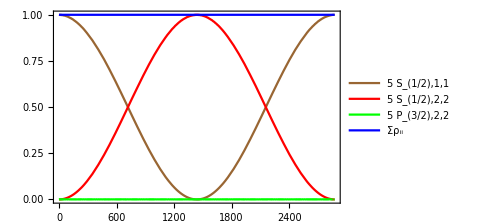

```mathematica
(*--define the things we left generic for debugging--*)
dD1=D1MatElem;
dD2=D2MatElem;
γD1=ΓD1*10^-9;
γD2=ΓD2*10^-9;
Ε1=10√(2/(c ϵ0)IsatD2SI) /GHz;
Ω1=Ε1 d[1,3,1]/ℏ;
Ε2=Ω1 /(d[3,2,2]/ℏ);
(*--setup the numerical solver--*)
Ωeff=Abs[((Ω1 Ω1)/(2 det))];
tmax=2π/Ωeff;
rho=Flatten@Table[Subscript[ρ, k,l][t],{l,1,dim},{k,l,dim}];
rho0=Array[0&,dim(dim+1)/2];
rho0[[1]]=1;
icEqs=Array[(rho/.t-> 0)[[#]]==rho0[[#]]&,Length[rho]];
{time,soln}= Timing[First@NDSolve[Flatten@Join[Eqs,icEqs], rho, {t,0,tmax},Method->Automatic,MaxStepFraction->0.001]];
Print["Time to run sim: ",time];
plt ={};
labels=Table[KetForm[states[[i]]],{i,Range[dim]}];
AppendTo[labels,"Σρ_ii"];
For[i=1, i<Length[soln]+1,i++,
AppendTo[plt,soln[[i,2]]]
];
{populations,coherences}=Indices[dim];
AppendTo[plt,Total[soln[[populations,2]]]];
AppendTo[populations,-1];
Plot[Evaluate[plt[[populations]]], {t, 0, tmax},PlotRange->All,PlotLegends->labels,PlotStyle->{Brown, Red,Green, Blue,Purple}]
```

## ^87 Rb - lambda-scheme Raman with spontaneous decay

```mathematica
(*states with n,L,J,F,mF, and angular frequency (energy) in 2π*GHz wrt ground state C.o.M. energy*)
ω5sOneHalfF2=2π*2.563005979089;
ω5sOneHalfF1=2π*-4.27167663181519;
ωD2=2π*384230.4844685;
ω5pThreeHalvesF0 =ωD2-2π*.3020738;
ω5pThreeHalvesF2=ωD2-2π*.072911332;
states={{5,0,1/2,1,1,ω5sOneHalfF1},{5,0,1/2,2,2,ω5sOneHalfF2},{5,1,3/2,2,2,ω5pThreeHalvesF2}};
{n,L,J,F,mF,ω}=Transpose@states;
dim=Length[states];

(*list of ground state hyperfine levels F*)
Fglist={1,2};

(*lists of field amplitudes, ang. frequencies, polarization, and angle in rad*)
Clear[Ε1,Ε2,γD1,γD2,dD1,dD2](*leave symbolic so it's easy to read the equations*);
det =2π*1;(*detuning. must be finite, but can be arbitrarily small... where does the 1/0 come from?*)
Efields={{Ε1,ω5pThreeHalvesF2-ω5sOneHalfF1-det,1,0},{Ε2,ω5pThreeHalvesF2-ω5sOneHalfF2-det, 0,0}};
{Ep,ωp,q,θ}=Transpose@Efields;
dimE=Length[Ep];

(*--things that depend on a pair of state indices j and k--*)
E1FineReduced[j_,k_]:=Switch[Sort[{{n[[j]],L[[j]],J[[j]]},{n[[k]],L[[k]],J[[k]]}}],{{5,0,1/2},{5,1,1/2}},dD1,{{5,0,1/2},{5,1,3/2}},dD2,_,0];(*get hardcoded D1 or D2 line reduced dipole matrix element.*)

d[m_,n_,p_]:=Module[{j,k},
{j,k}=Sort[{m,n}];(*because the matrix element is real, it is equal to its complex conjugate. Hence, when the state labels are reversed the value return is the same.*)
Quiet[(-1)^(1+INuc+J[[k]]+F[[j]])√(2F[[j]]+1)SixJSymbol[{J[[j]],INuc,F[[j]]},{F[[k]],1,J[[k]]}]ClebschGordan[{F[[j]],mF[[j]]},{1,q[[p]]},{F[[k]],mF[[k]]}]E1FineReduced[j,k]]
](*the hyperfine dipole matrix element.TODO: make general by including the Wigner D to allow rotations*)

γE1[j_,k_]:=Switch[Sort[{{n[[j]],L[[j]],J[[j]]},{n[[k]],L[[k]],J[[k]]}}],{{5,0,1/2},{5,1,1/2}},γD1,{{5,0,1/2},{5,1,3/2}},γD2,_,0];(*get hardcoded D1 or D2 line natural linewidth.*)

(*branching factor from an upper state k to j*)
b[{J_,F_,mF_},{JJ_,FF_,mFF_}]:=Quiet[(2F+1)SixJSymbol[{J,INuc,F},{FF,1,JJ}]^2 ClebschGordan[{F,mF},{1,mFF-mF},{FF,mFF}]^2];

(*decay from state k to j*)
γ[j_,k_]:=γE1[j,k](b[{J[[j]],F[[j]],mF[[j]]},{J[[k]],F[[k]],mF[[k]]}]/Total[Flatten[Table[Table[b[{J[[1]],Fg,mFg},{J[[k]],F[[k]],mF[[k]]}],{mFg,Range[-Fg,Fg]}],{Fg,Fglist}]]]);

Δ[p_,k_,j_]:=ωp[[p]]-(ω[[k]]-ω[[j]]);
(*terms with detunings of greater order of magnitude (GHz) than this will be dropped*)
drop=OoM[10]+1;(*GHz*)
Eqs = MEqs[states,Ep,Δ,d,γ,drop];(*generate the differential equations*)
"The equations to be solved:"
For[i=1,i<Length[Eqs]+1,i++,
Print[Eqs[[i]]//Expand//TraditionalForm]
]
```

The equations to be solved:

ρ_(1,1)'(t)==(0.-1.68359×10^33 ⅈ) dD2 Ε1 ⅇ^((0.+6.28319 ⅈ) t) Conjugate[ρ_(3,1)(t)]+(0.+1.68359×10^33 ⅈ) dD2 ⅇ^((0.-6.28319 ⅈ) t) Conjugate[Ε1] ρ_(3,1)(t)+0.5 γD2 ρ_(3,3)(t)

ρ_(2,1)'(t)==(0.-1.68359×10^33 ⅈ) dD2 Ε1 ⅇ^((0.+6.28319 ⅈ) t) Conjugate[ρ_(3,2)(t)]-(0.+1.37464×10^33 ⅈ) dD2 ⅇ^((0.-6.28319 ⅈ) t) Conjugate[Ε2] ρ_(3,1)(t)

ρ_(3,1)'(t)==(0.-1.68359×10^33 ⅈ) dD2 Ε1 ⅇ^((0.+6.28319 ⅈ) t) Conjugate[ρ_(3,3)(t)]+(0.+1.68359×10^33 ⅈ) dD2 Ε1 ⅇ^((0.+6.28319 ⅈ) t) ρ_(1,1)(t)-(0.+1.37464×10^33 ⅈ) dD2 Ε2 ⅇ^((0.+6.28319 ⅈ) t) ρ_(2,1)(t)-0.416667 γD2 ρ_(3,1)(t)

ρ_(2,2)'(t)==(0.+1.37464×10^33 ⅈ) dD2 Ε2 ⅇ^((0.+6.28319 ⅈ) t) Conjugate[ρ_(3,2)(t)]-(0.+1.37464×10^33 ⅈ) dD2 ⅇ^((0.-6.28319 ⅈ) t) Conjugate[Ε2] ρ_(3,2)(t)+0.333333 γD2 ρ_(3,3)(t)

ρ_(3,2)'(t)==(0.+1.68359×10^33 ⅈ) dD2 Ε1 ⅇ^((0.+6.28319 ⅈ) t) Conjugate[ρ_(2,1)(t)]+(0.+1.37464×10^33 ⅈ) dD2 Ε2 ⅇ^((0.+6.28319 ⅈ) t) Conjugate[ρ_(3,3)(t)]-(0.+1.37464×10^33 ⅈ) dD2 Ε2 ⅇ^((0.+6.28319 ⅈ) t) ρ_(2,2)(t)-0.416667 γD2 ρ_(3,2)(t)

ρ_(3,3)'(t)==(0.+1.68359×10^33 ⅈ) dD2 Ε1 ⅇ^((0.+6.28319 ⅈ) t) Conjugate[ρ_(3,1)(t)]-(0.+1.68359×10^33 ⅈ) dD2 ⅇ^((0.-6.28319 ⅈ) t) Conjugate[Ε1] ρ_(3,1)(t)-(0.+1.37464×10^33 ⅈ) dD2 Ε2 ⅇ^((0.+6.28319 ⅈ) t) Conjugate[ρ_(3,2)(t)]+(0.+1.37464×10^33 ⅈ) dD2 ⅇ^((0.-6.28319 ⅈ) t) Conjugate[Ε2] ρ_(3,2)(t)-(0.833333+0. ⅈ) γD2 ρ_(3,3)(t)

Time to run sim: 7.23438

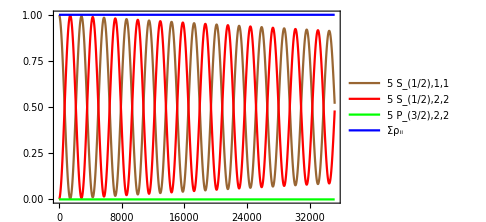

```mathematica
(*--define the things we left generic for debugging--*)
dD1=D1MatElem;
dD2=D2MatElem;
γD1=ΓD1*10^-9;
γD2=ΓD2*10^-9;
Ε1=10√(2/(c ϵ0)IsatD2SI) /GHz;
Ω1=Ε1 d[1,3,1]/ℏ;
Ε2=Ω1 /(d[3,2,2]/ℏ);
(*--setup the numerical solver--*)
Ωeff=Abs[((Ω1 Ω2)/(2 det))];
tmax=10*2π/Ωeff;
rho=Flatten@Table[Subscript[ρ, k,l][t],{l,1,dim},{k,l,dim}];
rho0=Array[0&,dim(dim+1)/2];
rho0[[1]]=1;
icEqs=Array[(rho/.t-> 0)[[#]]==rho0[[#]]&,Length[rho]];
{time,soln}= Timing[First@NDSolve[Flatten@Join[Eqs,icEqs], rho, {t,0,tmax},Method->Automatic,MaxStepFraction->0.001]];
Print["Time to run sim: ",time];
plt ={};
labels=Table[KetForm[states[[i]]],{i,Range[dim]}];
AppendTo[labels,"Σρ_ii"];
For[i=1, i<Length[soln]+1,i++,
AppendTo[plt,soln[[i,2]]]
];
{populations,coherences}=Indices[dim];
AppendTo[plt,Total[soln[[populations,2]]]];
AppendTo[populations,-1];
Plot[Evaluate[plt[[populations]]], {t, 0, tmax},PlotRange->All,PlotLegends->labels,PlotStyle->{Brown, Red,Green, Blue,Purple}]
```

## ^87 Rb - D1 optical pumping - test with only F=1,F’=1 levels

Run the setup cell to define the equation builder.

```mathematica
(*states with n,L,J,F,mF, and angular frequency (energy) in 2π*GHz wrt ground state C.o.M. energy*)

Fglist={1}(*Range[Abs[INuc-1/2],INuc+1/2]*);(*list of ground state hyperfine levels F*)
Fe1list=Fglist(*Range[Abs[INuc-1/2],INuc+1/2]*);
Fe2list={2};(*Range[Abs[INuc-3/2],INuc+3/2]*);
FivePThreeHalves=Flatten[Table[Table[{5,1,3/2,f,mf},{mf,Range[-f,f]}],{f,Fe2list}(*Range[Abs[INuc-3/2],INuc+3/2]}*)],1];
FivePOneHalf=Flatten[Table[Table[{5,1,1/2,f,mf},{mf,Range[-f,f]}],{f,Fe1list}],1];
FiveSOneHalf=Flatten[Table[Table[{5,0,1/2,f,mf},{mf,Range[-f,f]}],{f,Fglist}],1];
states=Join[FiveSOneHalf,FivePOneHalf(*,FivePThreeHalves*)];
{n,L,J,F,mF}=Transpose@states;
"Total number of states:"
dim=Length[states]

(*the energy of each state*)
ω=Table[2π Rb87fGHz[states[[i]][[;;4]]],{i,Range[dim]}];

(*lists of field amplitudes, ang. frequencies, polarization, and angle in rad*)
Clear[Ε1,Ε2,γD1,γD2,dD1,dD2](*leave symbolic so it's easy to read the equations*);

(*--define numerical constants--*)
dD1=D1MatElem;
dD2=D2MatElem;
γD1=ΓD1*10^-9;
γD2=ΓD2*10^-9;
Ε1=Ε2=.1√(2/(c ϵ0)IsatD1SI) /GHz;

det =2π*10^-9;(*detuning. must be finite, but can be arbitrarily small... where does the 1/0 come from?*)
Efields={{Ε1,2π(Rb87fGHz[{5,1,1/2,1}]-Rb87fGHz[{5,0,1/2,1}]-det),0,0}(*,{Ε2,2π(Rb87fGHz[{5,1,3/2,2}]-Rb87fGHz[{5,0,1/2,2}])-det, 0,0}*)};
{Ep,ωp,q,θ}=Transpose@Efields;
dimE=Length[Ep];

(*--things that depend on a pair of state indices j and k--*)
E1FineReduced[j_,k_]:=Switch[Sort[{{n[[j]],L[[j]],J[[j]]},{n[[k]],L[[k]],J[[k]]}}],{{5,0,1/2},{5,1,1/2}},dD1,{{5,0,1/2},{5,1,3/2}},dD2,_,0];(*get hardcoded D1 or D2 line reduced dipole matrix element.*)

d[m_,n_,p_]:=Module[{j,k},
{j,k}=Sort[{m,n}];(*because the matrix element is real, it is equal to its complex conjugate. Hence, when the state labels are reversed the value return is the same.*)
Quiet[(-1)^(1+INuc+J[[k]]+F[[j]])√(2F[[j]]+1)SixJSymbol[{J[[j]],INuc,F[[j]]},{F[[k]],1,J[[k]]}]ClebschGordan[{F[[j]],mF[[j]]},{1,q[[p]]},{F[[k]],mF[[k]]}]E1FineReduced[j,k]]
](*the hyperfine dipole matrix element.TODO: make general by including the Wigner D to allow rotations*)

γE1[j_,k_]:=Switch[Sort[{{n[[j]],L[[j]],J[[j]]},{n[[k]],L[[k]],J[[k]]}}],{{5,0,1/2},{5,1,1/2}},γD1,{{5,0,1/2},{5,1,3/2}},γD2,_,0];(*get hardcoded D1 or D2 line natural linewidth.*)

(*branching factor from an upper state k to j*)
b[{J_,F_,mF_},{JJ_,FF_,mFF_}]:=Quiet[(2F+1)SixJSymbol[{J,INuc,F},{FF,1,JJ}]^2 ClebschGordan[{F,mF},{1,mFF-mF},{FF,mFF}]^2];

(*pre-evaluate b values*)
Table[Subscript[bb, J[[j]],F[[j]],mF[[j]],J[[k]],F[[k]],mF[[k]]]=b[{J[[j]],F[[j]],mF[[j]]},{J[[k]],F[[k]],mF[[k]]}],{j,Range[dim]},{k,Range[j,dim]}];

(*decay from state k to j*)
γ[j_,k_]:=γE1[j,k](Subscript[bb, J[[j]],F[[j]],mF[[j]],J[[k]],F[[k]],mF[[k]]]/Total[Flatten[Table[Subscript[bb, J[[1]],Fg,mFg,J[[k]],F[[k]],mF[[k]]],{Fg,Fglist},{mFg,Range[-Fg,Fg]}],1]]);
(*γ[j_,k_]:=γE1[j,k](b[{J[[j]],F[[j]],mF[[j]]},{J[[k]],F[[k]],mF[[k]]}]/Total[Flatten[Table[Table[b[{J[[1]],Fg,mFg},{J[[k]],F[[k]],mF[[k]]}],{mFg,Range[-Fg,Fg]}],{Fg,Fglist}]]]);*)

Δ[p_,k_,j_]:=ωp[[p]]-(ω[[k]]-ω[[j]]);

(*pre-evaluate γ, d, and Δ values which we can "look up" by index*)
Table[γlookup[j,k]=γ[j,k],{j,Range[dim]},{k,Range[j,dim]}];
Table[dlookup[j,k,p]=d[j,k,p],{p,Range[dimE]},{j,Range[dim]},{k,Range[dim]}];
Table[Δlookup[p,k,j]=Δ[p,k,j],{p,Range[dimE]},{j,Range[dim]},{k,Range[dim]}];

(*terms with detunings of greater order of magnitude (GHz) than this will be dropped*)
drop=OoM[10]+1;(*GHz*)

(*equations to exclude for an approximate but much faster result*)
gExclude=Flatten[Table[{k,j},{j,Range[3]},{k,Range[j+1,3]}],1];(*coherences betweeen  5S1/2 hyperfine states*)
eExclude=Flatten[Table[{k,j},{j,Range[4,6]},{k,Range[j+1,6]}],1];(*coherences betweeen  5P1/2 hyperfine states*)
exclude=Join[gExclude,eExclude];

Eqs = MEqs[states,Ep,Δlookup,dlookup,γlookup,drop,exclude];(*generate the differential equations*)
"Number of equations"
Eqs//Length
"The equations to be solved:"
For[i=1,i<Length[Eqs]+1,i++,
Print[Eqs[[i]]//Expand//TraditionalForm]
]
```

Total number of states:

6

Number of equations

15

The equations to be solved:

ρ_(1,1)'(t)==(0.-0.000453346 ⅈ) ⅇ^((0.+4.00469×10^-8 ⅈ) t) Conjugate[ρ_(4,1)(t)]+(0.+0.000453346 ⅈ) ⅇ^((0.-4.00469×10^-8 ⅈ) t) ρ_(4,1)(t)+0.0180541 ρ_(4,4)(t)+0.0180541 ρ_(5,5)(t)+(0.+0. ⅈ)

ρ_(2,2)'(t)==0.0180541 ρ_(4,4)(t)+0.0180541 ρ_(6,6)(t)+(0.+0. ⅈ)

ρ_(3,3)'(t)==(0.+0.000453346 ⅈ) ⅇ^((0.+4.00469×10^-8 ⅈ) t) Conjugate[ρ_(6,3)(t)]-(0.+0.000453346 ⅈ) ⅇ^((0.-4.00469×10^-8 ⅈ) t) ρ_(6,3)(t)+0.0180541 ρ_(5,5)(t)+0.0180541 ρ_(6,6)(t)+(0.+0. ⅈ)

ρ_(4,4)'(t)==(0.+0.000453346 ⅈ) ⅇ^((0.+4.00469×10^-8 ⅈ) t) Conjugate[ρ_(4,1)(t)]-(0.+0.000453346 ⅈ) ⅇ^((0.-4.00469×10^-8 ⅈ) t) ρ_(4,1)(t)-0.0361082 ρ_(4,4)(t)+(0.+0. ⅈ)

ρ_(5,5)'(t)==-0.0361082 ρ_(5,5)(t)+(0.+0. ⅈ)

ρ_(6,6)'(t)==(0.-0.000453346 ⅈ) ⅇ^((0.+4.00469×10^-8 ⅈ) t) Conjugate[ρ_(6,3)(t)]+(0.+0.000453346 ⅈ) ⅇ^((0.-4.00469×10^-8 ⅈ) t) ρ_(6,3)(t)-0.0361082 ρ_(6,6)(t)+(0.+0. ⅈ)

ρ_(4,1)'(t)==(0.-0.000453346 ⅈ) ⅇ^((0.+4.00469×10^-8 ⅈ) t) Conjugate[ρ_(4,4)(t)]+(0.+0.000453346 ⅈ) ⅇ^((0.+4.00469×10^-8 ⅈ) t) ρ_(1,1)(t)-0.0180541 ρ_(4,1)(t)+(0.+0. ⅈ)

ρ_(5,1)'(t)==-0.0180541 ρ_(5,1)(t)+(0.+0. ⅈ)

ρ_(6,1)'(t)==-0.0180541 ρ_(6,1)(t)+(0.+0. ⅈ)

ρ_(4,2)'(t)==-0.0180541 ρ_(4,2)(t)+(0.+0. ⅈ)

ρ_(5,2)'(t)==-0.0180541 ρ_(5,2)(t)+(0.+0. ⅈ)

ρ_(6,2)'(t)==-0.0180541 ρ_(6,2)(t)+(0.+0. ⅈ)

ρ_(4,3)'(t)==-0.0180541 ρ_(4,3)(t)+(0.+0. ⅈ)

ρ_(5,3)'(t)==-0.0180541 ρ_(5,3)(t)+(0.+0. ⅈ)

ρ_(6,3)'(t)==(0.+0.000453346 ⅈ) ⅇ^((0.+4.00469×10^-8 ⅈ) t) Conjugate[ρ_(6,6)(t)]-(0.+0.000453346 ⅈ) ⅇ^((0.+4.00469×10^-8 ⅈ) t) ρ_(3,3)(t)-0.0180541 ρ_(6,3)(t)+(0.+0. ⅈ)

```mathematica
(*--setup for the numerical solver--*)

(*the list of populations and coherences we're including, in the same order as in Eqs*)
rho=Join[Table[Subscript[ρ, k,k][t],{k,Range[dim]}],Complement[Flatten[Table[Subscript[ρ, k,l][t],{l,1,dim},{k,l+1,dim}],1],Array[Subscript[ρ, exclude[[#,1]],exclude[[#,2]]][t]&,Length[exclude]]]];
rho0=Array[0&,Length[rho]];
rho0[[{1,2,3}]]=1/3;
Ω1=Ε1 d[1,4,1]/ℏ;
(*Ω2=Ε2 d[8,17,2]/ℏ;*)
Ωeff=Abs[Ω1] ;
Print["Effective rabi frequency = 2π*",Ωeff GHz/10^6," MHz"]
tmax=100*2π/Ωeff;
```

Effective rabi frequency = 2π*0.906691 MHz

Time to run sim: 0.03125

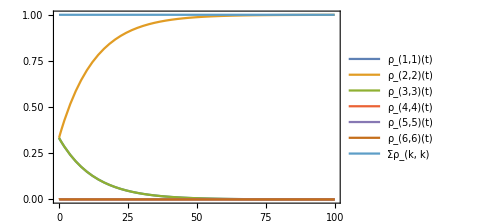

```mathematica
icEqs=Array[(rho/.t-> 0)[[#]]==rho0[[#]]&,Length[rho]];
{time,soln}= Timing[First@NDSolve[Flatten@Join[Eqs,icEqs], rho, {t,0,tmax},Method->Automatic]](*,MaxStepFraction->0.001]]*);
Print["Time to run sim: ",time];
labels=rho[[;;dim]];
AppendTo[labels,"Σρ_(k, k)"];
lines=Re[(rho/.soln)[[;;dim]]];
AppendTo[lines,Total[(rho/.soln)[[;;dim]]]];
(*Plot[Evaluate[lines], {t, 0,tmax },PlotRange->All,PlotLegends->labels]*)
Plot[Evaluate[lines/.t->τ (2π)/Ωeff], {τ, 0,tmax Ωeff/(2π)},PlotRange->All,PlotLegends->labels]
```

## ^87 Rb - D2 damped Rabi oscillations F=1->F’=0

With linear polarization aligned to the quantization axis, and population initially in F=1,m=0, the population will gradually be pumped to the m=+/-1 dark states.

```mathematica
(*states with n,L,J,F,mF, and angular frequency (energy) in 2π*GHz wrt ground state C.o.M. energy*)

Fglist={1}(*Range[Abs[INuc-1/2],INuc+1/2]*);(*list of ground state hyperfine levels F*)
Fe1list=Fglist(*Range[Abs[INuc-1/2],INuc+1/2]*);
Fe2list={0};(*Range[Abs[INuc-3/2],INuc+3/2]*);
FivePThreeHalves=Flatten[Table[Table[{5,1,3/2,f,mf},{mf,Range[-f,f]}],{f,Fe2list}(*Range[Abs[INuc-3/2],INuc+3/2]}*)],1];
FivePOneHalf=Flatten[Table[Table[{5,1,1/2,f,mf},{mf,Range[-f,f]}],{f,Fe1list}],1];
FiveSOneHalf=Flatten[Table[Table[{5,0,1/2,f,mf},{mf,Range[-f,f]}],{f,Fglist}],1];
states=Join[FiveSOneHalf,FivePThreeHalves];
{n,L,J,F,mF}=Transpose@states;
"Total number of states:"
dim=Length[states]

(*the energy of each state*)
ω=Table[2π Rb87fGHz[states[[i]][[;;4]]],{i,Range[dim]}];

(*lists of field amplitudes, ang. frequencies, polarization, and angle in rad*)
Clear[Ε1,Ε2,γD1,γD2,dD1,dD2](*leave symbolic so it's easy to read the equations*);

det =2π*10^-9;(*detuning. must be finite, but can be arbitrarily small... where does the 1/0 come from?*)
Efields={{Ε1,2π(Rb87fGHz[{5,1,3/2,0}]-Rb87fGHz[{5,0,1/2,1}]-det),0,0}(*,{Ε2,2π(Rb87fGHz[{5,1,3/2,2}]-Rb87fGHz[{5,0,1/2,2}])-det, 0,0}*)};
{Ep,ωp,q,θ}=Transpose@Efields;
dimE=Length[Ep];

(*--things that depend on a pair of state indices j and k--*)
E1FineReduced[j_,k_]:=Switch[Sort[{{n[[j]],L[[j]],J[[j]]},{n[[k]],L[[k]],J[[k]]}}],{{5,0,1/2},{5,1,1/2}},dD1,{{5,0,1/2},{5,1,3/2}},dD2,_,0];(*get hardcoded D1 or D2 line reduced dipole matrix element.*)

dRotated[m_,n_,p_]:=Module[{j,k},
{j,k}=Sort[{m,n}];(*because the matrix element is real, it is equal to its complex conjugate. Hence, d[m,n,p]=d[n,m,p].*)
Quiet[(Sum[WignerD[{F[[k]],mF[[k]],mFk},θ[[p]]]WignerD[{F[[j]],mFj,mF[[j]]},θ[[p]]]ClebschGordan[{F[[j]],mFj},{1,q[[p]]},{F[[k]],mFk}],{mFk,Range[-F[[k]],F[[k]]]},{mFj,Range[-F[[j]],F[[j]]]}])(-1)^(1+INuc+J[[k]]+F[[j]])√(2F[[j]]+1)SixJSymbol[{J[[j]],INuc,F[[j]]},{F[[k]],1,J[[k]]}]E1FineReduced[j,k]]
]

γE1[j_,k_]:=Switch[Sort[{{n[[j]],L[[j]],J[[j]]},{n[[k]],L[[k]],J[[k]]}}],{{5,0,1/2},{5,1,1/2}},γD1,{{5,0,1/2},{5,1,3/2}},γD2,_,0];(*get hardcoded D1 or D2 line natural linewidth.*)

(*branching factor from an upper state k to j*)
b[{J_,F_,mF_},{JJ_,FF_,mFF_}]:=Quiet[(2F+1)SixJSymbol[{J,INuc,F},{FF,1,JJ}]^2 ClebschGordan[{F,mF},{1,mFF-mF},{FF,mFF}]^2];

(*pre-evaluate b values*)
Table[Subscript[bb, J[[j]],F[[j]],mF[[j]],J[[k]],F[[k]],mF[[k]]]=b[{J[[j]],F[[j]],mF[[j]]},{J[[k]],F[[k]],mF[[k]]}],{j,Range[dim]},{k,Range[j,dim]}];

(*decay from state k to j*)
γ[j_,k_]:=γE1[j,k](Subscript[bb, J[[j]],F[[j]],mF[[j]],J[[k]],F[[k]],mF[[k]]]/Total[Flatten[Table[Subscript[bb, J[[1]],Fg,mFg,J[[k]],F[[k]],mF[[k]]],{Fg,Fglist},{mFg,Range[-Fg,Fg]}],1]]);
(*γ[j_,k_]:=γE1[j,k](b[{J[[j]],F[[j]],mF[[j]]},{J[[k]],F[[k]],mF[[k]]}]/Total[Flatten[Table[Table[b[{J[[1]],Fg,mFg},{J[[k]],F[[k]],mF[[k]]}],{mFg,Range[-Fg,Fg]}],{Fg,Fglist}]]]);*)

Δ[p_,k_,j_]:=ωp[[p]]-(ω[[k]]-ω[[j]]);

(*pre-evaluate γ, d, and Δ values which we can "look up" by index*)
Table[γlookup[j,k]=γ[j,k],{j,Range[dim]},{k,Range[j,dim]}];
Table[dlookup[j,k,p]=dRotated[j,k,p],{p,Range[dimE]},{j,Range[dim]},{k,Range[dim]}];
Table[Δlookup[p,k,j]=Δ[p,k,j],{p,Range[dimE]},{j,Range[dim]},{k,Range[dim]}];

(*terms with detunings of greater order of magnitude (GHz) than this will be dropped*)
drop=OoM[10]+1;(*GHz*)

(*equations to exclude for an approximate but much faster result*)
gExclude=Flatten[Table[{k,j},{j,Range[3]},{k,Range[j+1,3]}],1];(*coherences betweeen  5S1/2 hyperfine states*)
eExclude=Flatten[Table[{k,j},{j,Range[4,6]},{k,Range[j+1,6]}],1];(*coherences betweeen  5P1/2 hyperfine states*)
exclude=Join[gExclude,eExclude];

Eqs = MEqs[states,Ep,Δlookup,dlookup,γlookup,drop,exclude];(*generate the differential equations*)
"Number of equations"
Eqs//Length
"The equations to be solved:"
For[i=1,i<Length[Eqs]+1,i++,
Print[Eqs[[i]]//Expand//TraditionalForm]
]
```

Total number of states:

4

Number of equations

7

The equations to be solved:

ρ_(1,1)'(t)==1/3 γD2 ρ_(4,4)(t)+(0.+0. ⅈ)

ρ_(2,2)'(t)==(0.+1.37464×10^33 ⅈ) dD2 Ε1 ⅇ^((0.+3.95812×10^-8 ⅈ) t) Conjugate[ρ_(4,2)(t)]-(0.+1.37464×10^33 ⅈ) dD2 ⅇ^((0.-3.95812×10^-8 ⅈ) t) Conjugate[Ε1] ρ_(4,2)(t)+1/3 γD2 ρ_(4,4)(t)

ρ_(3,3)'(t)==1/3 γD2 ρ_(4,4)(t)+(0.+0. ⅈ)

ρ_(4,4)'(t)==(0.-1.37464×10^33 ⅈ) dD2 Ε1 ⅇ^((0.+3.95812×10^-8 ⅈ) t) Conjugate[ρ_(4,2)(t)]+(0.+1.37464×10^33 ⅈ) dD2 ⅇ^((0.-3.95812×10^-8 ⅈ) t) Conjugate[Ε1] ρ_(4,2)(t)-γD2 ρ_(4,4)(t)

ρ_(4,1)'(t)==-1/2 γD2 ρ_(4,1)(t)+(0.+0. ⅈ)

ρ_(4,2)'(t)==(0.+1.37464×10^33 ⅈ) dD2 Ε1 ⅇ^((0.+3.95812×10^-8 ⅈ) t) Conjugate[ρ_(4,4)(t)]-(0.+1.37464×10^33 ⅈ) dD2 Ε1 ⅇ^((0.+3.95812×10^-8 ⅈ) t) ρ_(2,2)(t)-1/2 γD2 ρ_(4,2)(t)

ρ_(4,3)'(t)==-1/2 γD2 ρ_(4,3)(t)+(0.+0. ⅈ)

```mathematica
(*--define numerical constants--*)
dD1=D1MatElem;
dD2=D2MatElem;
γD1=ΓD1*10^-9;
γD2=ΓD2*10^-9;
Ε1=Ε2=10√(2/(c ϵ0)IsatD2SI) /GHz;

(*--setup for the numerical solver--*)

(*the list of populations and coherences we're including, in the same order as in Eqs*)
rho=Join[Table[Subscript[ρ, k,k][t],{k,Range[dim]}],Complement[Flatten[Table[Subscript[ρ, k,l][t],{l,1,dim},{k,l+1,dim}],1],Array[Subscript[ρ, exclude[[#,1]],exclude[[#,2]]][t]&,Length[exclude]]]];
rho0=Array[0&,Length[rho]];
(*rho0[[{1,2,3}]]=1/3;*)
rho0[[2]]=1;
Ω1=Ε1 d[2,4,1]/ℏ;
(*Ω2=Ε2 d[8,17,2]/ℏ;*)
Ωeff=Abs[Ω1] ;
Print["Effective rabi frequency = 2π*",Ωeff/(2π) GHz/MHz," MHz"]
tmax=10*2π/Ωeff;
```

Effective rabi frequency = 2π*21.5398 MHz

Time to run sim: 0.

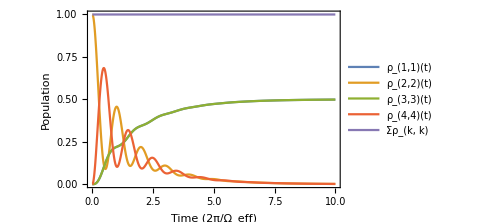

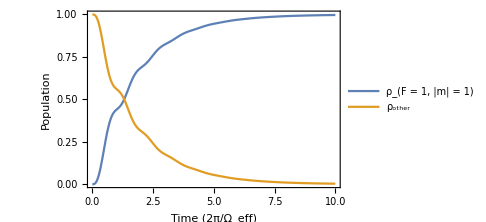

```mathematica
icEqs=Array[(rho/.t-> 0)[[#]]==rho0[[#]]&,Length[rho]];
{time,soln}= Timing[First@NDSolve[Flatten@Join[Eqs,icEqs], rho, {t,0,tmax},Method->Automatic]](*,MaxStepFraction->0.001]]*);
Print["Time to run sim: ",time];
labels=rho[[;;dim]];
AppendTo[labels,"Σρ_(k, k)"];
lines=Re[(rho/.soln)[[;;dim]]];
AppendTo[lines,Total[(rho/.soln)[[;;dim]]]];
(*Plot[Evaluate[lines], {t, 0,tmax },PlotRange->All,PlotLegends->labels]*)
Plot[Evaluate[lines/.t->τ (2π)/Ωeff], {τ, 0,tmax Ωeff/(2π)},PlotRange->All,PlotLegends->labels,FrameLabel->{"Time (2π/Ω_eff)","Population"}]
Plot[Evaluate[{Total[lines[[{1,3}]]],Total[lines[[{2,4}]]]}/.t->τ (2π)/Ωeff], {τ, 0,tmax Ωeff/(2π)},PlotRange->All,PlotLegends->{"ρ_(F = 1, |m| = 1)","ρ_other"},FrameLabel->{"Time (2π/Ω_eff)","Population"}]
```

## ^87 Rb - D2 Rabi oscillations F=1->F’=0, rotated dipole operator

Tilting the linear polarization at 54.7 deg. wrt the quantization axis will equalize the three transition rates, whereas the σ transitions rates are 0 for linear polarization aligned to the quantization axis. However, the Rabi frequencies for the σ transitions will be π out of phase with each other, while the σ+ Rabi frequency will be in phase with the π Rabi frequency. As a result, a partial EIT effect will occur leading to a maximum population inversion of 1/2.

```mathematica
(*states with n,L,J,F,mF, and angular frequency (energy) in 2π*GHz wrt ground state C.o.M. energy*)

Fglist={1}(*Range[Abs[INuc-1/2],INuc+1/2]*);(*list of ground state hyperfine levels F*)
Fe1list=Fglist(*Range[Abs[INuc-1/2],INuc+1/2]*);
Fe2list={0};(*Range[Abs[INuc-3/2],INuc+3/2]*);
FivePThreeHalves=Flatten[Table[Table[{5,1,3/2,f,mf},{mf,Range[-f,f]}],{f,Fe2list}(*Range[Abs[INuc-3/2],INuc+3/2]}*)],1];
FivePOneHalf=Flatten[Table[Table[{5,1,1/2,f,mf},{mf,Range[-f,f]}],{f,Fe1list}],1];
FiveSOneHalf=Flatten[Table[Table[{5,0,1/2,f,mf},{mf,Range[-f,f]}],{f,Fglist}],1];
states=Join[FiveSOneHalf,FivePThreeHalves];
{n,L,J,F,mF}=Transpose@states;
"Total number of states:"
dim=Length[states]

(*the energy of each state*)
ω=Table[2π Rb87fGHz[states[[i]][[;;4]]],{i,Range[dim]}];

(*lists of field amplitudes, ang. frequencies, polarization, and angle in rad*)
Clear[Ε1,Ε2,γD1,γD2,dD1,dD2](*leave symbolic so it's easy to read the equations*);

det =2π*10^-10;(*detuning. must be finite, but can be arbitrarily small... where does the 1/0 come from?*)
Efields={{Ε1,2π(Rb87fGHz[{5,1,3/2,0}]-Rb87fGHz[{5,0,1/2,1}]-det),0,54.7/180 π}(*,{Ε2,2π(Rb87fGHz[{5,1,3/2,2}]-Rb87fGHz[{5,0,1/2,2}])-det, 0,0}*)};
{Ep,ωp,q,θ}=Transpose@Efields;
dimE=Length[Ep];

(*--things that depend on a pair of state indices j and k--*)
E1FineReduced[j_,k_]:=Switch[Sort[{{n[[j]],L[[j]],J[[j]]},{n[[k]],L[[k]],J[[k]]}}],{{5,0,1/2},{5,1,1/2}},dD1,{{5,0,1/2},{5,1,3/2}},dD2,_,0];(*get hardcoded D1 or D2 line reduced dipole matrix element.*)

dRotated[m_,n_,p_]:=Module[{j,k},
{j,k}=Sort[{m,n}];(*because the matrix element is real, it is equal to its complex conjugate. Hence, d[m,n,p]=d[n,m,p].*)
Quiet[(Sum[WignerD[{F[[k]],mF[[k]],mFk},θ[[p]]]WignerD[{F[[j]],mFj,mF[[j]]},θ[[p]]]ClebschGordan[{F[[j]],mFj},{1,q[[p]]},{F[[k]],mFk}],{mFk,Range[-F[[k]],F[[k]]]},{mFj,Range[-F[[j]],F[[j]]]}])(-1)^(1+INuc+J[[k]]+F[[j]])√(2F[[j]]+1)SixJSymbol[{J[[j]],INuc,F[[j]]},{F[[k]],1,J[[k]]}]E1FineReduced[j,k]]
]

γE1[j_,k_]:=Switch[Sort[{{n[[j]],L[[j]],J[[j]]},{n[[k]],L[[k]],J[[k]]}}],{{5,0,1/2},{5,1,1/2}},γD1,{{5,0,1/2},{5,1,3/2}},γD2,_,0];(*get hardcoded D1 or D2 line natural linewidth.*)

(*branching factor from an upper state k to j*)
b[{J_,F_,mF_},{JJ_,FF_,mFF_}]:=Quiet[(2F+1)SixJSymbol[{J,INuc,F},{FF,1,JJ}]^2 ClebschGordan[{F,mF},{1,mFF-mF},{FF,mFF}]^2];

(*pre-evaluate b values*)
Table[Subscript[bb, J[[j]],F[[j]],mF[[j]],J[[k]],F[[k]],mF[[k]]]=b[{J[[j]],F[[j]],mF[[j]]},{J[[k]],F[[k]],mF[[k]]}],{j,Range[dim]},{k,Range[j,dim]}];

(*decay from state k to j*)
γ[j_,k_]:=γE1[j,k](Subscript[bb, J[[j]],F[[j]],mF[[j]],J[[k]],F[[k]],mF[[k]]]/Total[Flatten[Table[Subscript[bb, J[[1]],Fg,mFg,J[[k]],F[[k]],mF[[k]]],{Fg,Fglist},{mFg,Range[-Fg,Fg]}],1]]);
(*γ[j_,k_]:=γE1[j,k](b[{J[[j]],F[[j]],mF[[j]]},{J[[k]],F[[k]],mF[[k]]}]/Total[Flatten[Table[Table[b[{J[[1]],Fg,mFg},{J[[k]],F[[k]],mF[[k]]}],{mFg,Range[-Fg,Fg]}],{Fg,Fglist}]]]);*)

Δ[p_,k_,j_]:=ωp[[p]]-(ω[[k]]-ω[[j]]);

(*pre-evaluate γ, d, and Δ values which we can "look up" by index*)
Table[γlookup[j,k]=γ[j,k],{j,Range[dim]},{k,Range[j,dim]}];
Table[dlookup[j,k,p]=dRotated[j,k,p],{p,Range[dimE]},{j,Range[dim]},{k,Range[dim]}];
Table[Δlookup[p,k,j]=Δ[p,k,j],{p,Range[dimE]},{j,Range[dim]},{k,Range[dim]}];

(*terms with detunings of greater order of magnitude (GHz) than this will be dropped*)
drop=OoM[10]+1;(*GHz*)

(*equations to exclude for an approximate but much faster result*)
gExclude=Flatten[Table[{k,j},{j,Range[3]},{k,Range[j+1,3]}],1];(*coherences betweeen  5S1/2 hyperfine states*)
eExclude=Flatten[Table[{k,j},{j,Range[4,6]},{k,Range[j+1,6]}],1];(*coherences betweeen  5P1/2 hyperfine states*)
exclude=Join[gExclude,eExclude];

Eqs = MEqs[states,Ep,Δlookup,dlookup,γlookup,drop,exclude];(*generate the differential equations*)
"Number of equations"
Eqs//Length
"The equations to be solved:"
For[i=1,i<Length[Eqs]+1,i++,
Print[Eqs[[i]]//Expand//TraditionalForm]
]
```

Total number of states:

4

Number of equations

7

The equations to be solved:

ρ_(1,1)'(t)==(0.+7.93302×10^32 ⅈ) dD2 Ε1 ⅇ^((0.+4.19095×10^-9 ⅈ) t) Conjugate[ρ_(4,1)(t)]-(0.+7.93302×10^32 ⅈ) dD2 ⅇ^((0.-4.19095×10^-9 ⅈ) t) Conjugate[Ε1] ρ_(4,1)(t)+1/3 γD2 ρ_(4,4)(t)+(0.+0. ⅈ)

ρ_(2,2)'(t)==(0.+7.94348×10^32 ⅈ) dD2 Ε1 ⅇ^((0.+4.19095×10^-9 ⅈ) t) Conjugate[ρ_(4,2)(t)]-(0.+7.94348×10^32 ⅈ) dD2 ⅇ^((0.-4.19095×10^-9 ⅈ) t) Conjugate[Ε1] ρ_(4,2)(t)+1/3 γD2 ρ_(4,4)(t)+(0.+0. ⅈ)

ρ_(3,3)'(t)==(0.-7.93302×10^32 ⅈ) dD2 Ε1 ⅇ^((0.+4.19095×10^-9 ⅈ) t) Conjugate[ρ_(4,3)(t)]+(0.+7.93302×10^32 ⅈ) dD2 ⅇ^((0.-4.19095×10^-9 ⅈ) t) Conjugate[Ε1] ρ_(4,3)(t)+1/3 γD2 ρ_(4,4)(t)+(0.+0. ⅈ)

ρ_(4,4)'(t)==(0.-7.93302×10^32 ⅈ) dD2 Ε1 ⅇ^((0.+4.19095×10^-9 ⅈ) t) Conjugate[ρ_(4,1)(t)]-(0.+7.94348×10^32 ⅈ) dD2 Ε1 ⅇ^((0.+4.19095×10^-9 ⅈ) t) Conjugate[ρ_(4,2)(t)]+(0.+7.93302×10^32 ⅈ) dD2 Ε1 ⅇ^((0.+4.19095×10^-9 ⅈ) t) Conjugate[ρ_(4,3)(t)]+(0.+7.93302×10^32 ⅈ) dD2 ⅇ^((0.-4.19095×10^-9 ⅈ) t) Conjugate[Ε1] ρ_(4,1)(t)+(0.+7.94348×10^32 ⅈ) dD2 ⅇ^((0.-4.19095×10^-9 ⅈ) t) Conjugate[Ε1] ρ_(4,2)(t)-(0.+7.93302×10^32 ⅈ) dD2 ⅇ^((0.-4.19095×10^-9 ⅈ) t) Conjugate[Ε1] ρ_(4,3)(t)-γD2 ρ_(4,4)(t)

ρ_(4,1)'(t)==(0.+7.93302×10^32 ⅈ) dD2 Ε1 ⅇ^((0.+4.19095×10^-9 ⅈ) t) Conjugate[ρ_(4,4)(t)]-(0.+7.93302×10^32 ⅈ) dD2 Ε1 ⅇ^((0.+4.19095×10^-9 ⅈ) t) ρ_(1,1)(t)-1/2 γD2 ρ_(4,1)(t)+(0.+0. ⅈ)

ρ_(4,2)'(t)==(0.+7.94348×10^32 ⅈ) dD2 Ε1 ⅇ^((0.+4.19095×10^-9 ⅈ) t) Conjugate[ρ_(4,4)(t)]-(0.+7.94348×10^32 ⅈ) dD2 Ε1 ⅇ^((0.+4.19095×10^-9 ⅈ) t) ρ_(2,2)(t)-1/2 γD2 ρ_(4,2)(t)+(0.+0. ⅈ)

ρ_(4,3)'(t)==(0.-7.93302×10^32 ⅈ) dD2 Ε1 ⅇ^((0.+4.19095×10^-9 ⅈ) t) Conjugate[ρ_(4,4)(t)]+(0.+7.93302×10^32 ⅈ) dD2 Ε1 ⅇ^((0.+4.19095×10^-9 ⅈ) t) ρ_(3,3)(t)-1/2 γD2 ρ_(4,3)(t)+(0.+0. ⅈ)

```mathematica
(*--define numerical constants--*)
dD1=D1MatElem;
dD2=D2MatElem;
γD1=ΓD1*10^-9;
γD2=ΓD2*10^-9;
Ε1=Ε2=√(2/(c ϵ0)100000IsatD2SI) /GHz;

(*--setup for the numerical solver--*)

(*the list of populations and coherences we're including, in the same order as in Eqs*)
rho=Join[Table[Subscript[ρ, k,k][t],{k,Range[dim]}],Complement[Flatten[Table[Subscript[ρ, k,l][t],{l,1,dim},{k,l+1,dim}],1],Array[Subscript[ρ, exclude[[#,1]],exclude[[#,2]]][t]&,Length[exclude]]]];
rho0=Array[0&,Length[rho]];
(*rho0[[{1,2,3}]]=1/3;*)
rho0[[3]]=1;
Ω1=Ε1 d[2,4,1]/ℏ;
(*Ω2=Ε2 d[8,17,2]/ℏ;*)
Ωeff=Abs[Ω1] ;
Print["Effective rabi frequency = 2π*",Ωeff/(2π) GHz/MHz," MHz"]
tmax=10*2π/Ωeff;
```

Effective rabi frequency = 2π*681.148 MHz

Time to run sim: 0.015625

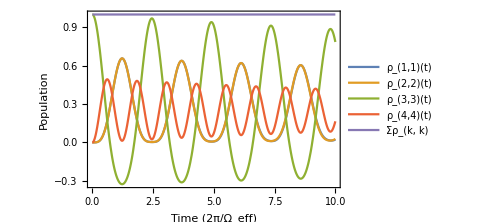

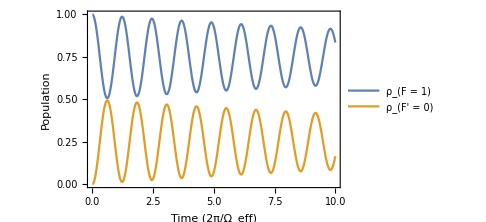

```mathematica
icEqs=Array[(rho/.t-> 0)[[#]]==rho0[[#]]&,Length[rho]];
{time,soln}= Timing[First@NDSolve[Flatten@Join[Eqs,icEqs], rho, {t,0,tmax},Method->Automatic]](*,MaxStepFraction->0.001]]*);
Print["Time to run sim: ",time];
labels=rho[[;;dim]];
AppendTo[labels,"Σρ_(k, k)"];
lines=Re[(rho/.soln)[[;;dim]]];
AppendTo[lines,Total[(rho/.soln)[[;;dim]]]];
(*Plot[Evaluate[lines], {t, 0,tmax },PlotRange->All,PlotLegends->labels]*)
Plot[Evaluate[lines/.t->τ (2π)/Ωeff], {τ, 0,tmax Ωeff/(2π)},PlotRange->All,PlotLegends->labels,FrameLabel->{"Time (2π/Ω_eff)","Population"}]
linesF1=Re[(rho/.soln)[[;;3]]];
linesF0=Re[(rho/.soln)[[4]]];
Plot[Evaluate[{Total[linesF1],linesF0}/.t->τ (2π)/Ωeff], {τ, 0,tmax Ωeff/(2π)},PlotRange->All,PlotLegends->{"ρ_(F = 1)","ρ_(F' = 0)"},FrameLabel->{"Time (2π/Ω_eff)","Population"}]
```

## ^87 Rb - D1 optical pumping with D2 repump

Optical pumping to the F=1,m=0 ground state. Linear pump light is resonant with F=1->F’=1, and linear repump light is resonant with F=2->F’=2

```mathematica
(*states with n,L,J,F,mF, and angular frequency (energy) in 2π*GHz wrt ground state C.o.M. energy*)

Fglist=Range[Abs[INuc-1/2],INuc+1/2];(*list of ground state hyperfine levels F*)
Fe1list=Range[Abs[INuc-1/2],INuc+1/2];
Fe2list=Range[Abs[INuc-3/2],INuc+3/2];
FivePThreeHalves=Flatten[Table[Table[{5,1,3/2,f,mf},{mf,Range[-f,f]}],{f,Fe2list}(*Range[Abs[INuc-3/2],INuc+3/2]}*)],1];
FivePOneHalf=Flatten[Table[Table[{5,1,1/2,f,mf},{mf,Range[-f,f]}],{f,Fe1list}],1];
FiveSOneHalf=Flatten[Table[Table[{5,0,1/2,f,mf},{mf,Range[-f,f]}],{f,Fglist}],1];
states=Join[FiveSOneHalf,FivePOneHalf,FivePThreeHalves];
{n,L,J,F,mF}=Transpose@states;
"Total number of states:"
dim=Length[states]

(*the energy of each state*)
ω=Table[2π Rb87fGHz[states[[i]][[;;4]]],{i,Range[dim]}];

(*lists of field amplitudes, ang. frequencies, polarization, and angle in rad*)
Clear[Εpump,Εrepump,γD1,γD2,dD1,dD2](*leave symbolic so it's easy to read the equations*);

det =2π*10^-10;(*detuning. must be finite, but can be arbitrarily small... where does the 1/0 come from?*)
Efields={{Εpump,2π(Rb87fGHz[{5,1,1/2,1}]-Rb87fGHz[{5,0,1/2,1}]-det),0,0},{Εrepump,2π(Rb87fGHz[{5,1,3/2,2}]-Rb87fGHz[{5,0,1/2,2}]-det),0,0}};
{Ep,ωp,q,θ}=Transpose@Efields;
dimE=Length[Ep];

(*--things that depend on a pair of state indices j and k--*)
E1FineReduced[j_,k_]:=Switch[Sort[{{n[[j]],L[[j]],J[[j]]},{n[[k]],L[[k]],J[[k]]}}],{{5,0,1/2},{5,1,1/2}},dD1,{{5,0,1/2},{5,1,3/2}},dD2,_,0];(*get hardcoded D1 or D2 line reduced dipole matrix element.*)

dRotated[m_,n_,p_]:=Module[{j,k},
{j,k}=Sort[{m,n}];(*because the matrix element is real, it is equal to its complex conjugate. Hence, d[m,n,p]=d[n,m,p].*)
Quiet[(Sum[WignerD[{F[[k]],mF[[k]],mFk},θ[[p]]]WignerD[{F[[j]],mFj,mF[[j]]},θ[[p]]]ClebschGordan[{F[[j]],mFj},{1,q[[p]]},{F[[k]],mFk}],{mFk,Range[-F[[k]],F[[k]]]},{mFj,Range[-F[[j]],F[[j]]]}])(-1)^(1+INuc+J[[k]]+F[[j]])√(2F[[j]]+1)SixJSymbol[{J[[j]],INuc,F[[j]]},{F[[k]],1,J[[k]]}]E1FineReduced[j,k]]
]

γE1[j_,k_]:=Switch[Sort[{{n[[j]],L[[j]],J[[j]]},{n[[k]],L[[k]],J[[k]]}}],{{5,0,1/2},{5,1,1/2}},γD1,{{5,0,1/2},{5,1,3/2}},γD2,_,0];(*get hardcoded D1 or D2 line natural linewidth.*)

(*branching factor from an upper state k to j*)
b[{J_,F_,mF_},{JJ_,FF_,mFF_}]:=Quiet[(2F+1)SixJSymbol[{J,INuc,F},{FF,1,JJ}]^2 ClebschGordan[{F,mF},{1,mFF-mF},{FF,mFF}]^2];

(*pre-evaluate b values*)
Table[Subscript[bb, J[[j]],F[[j]],mF[[j]],J[[k]],F[[k]],mF[[k]]]=b[{J[[j]],F[[j]],mF[[j]]},{J[[k]],F[[k]],mF[[k]]}],{j,Range[dim]},{k,Range[j,dim]}];

(*decay from state k to j*)
γ[j_,k_]:=γE1[j,k](Subscript[bb, J[[j]],F[[j]],mF[[j]],J[[k]],F[[k]],mF[[k]]]/Total[Flatten[Table[Subscript[bb, J[[1]],Fg,mFg,J[[k]],F[[k]],mF[[k]]],{Fg,Fglist},{mFg,Range[-Fg,Fg]}],1]]);
(*γ[j_,k_]:=γE1[j,k](b[{J[[j]],F[[j]],mF[[j]]},{J[[k]],F[[k]],mF[[k]]}]/Total[Flatten[Table[Table[b[{J[[1]],Fg,mFg},{J[[k]],F[[k]],mF[[k]]}],{mFg,Range[-Fg,Fg]}],{Fg,Fglist}]]]);*)

Δ[p_,k_,j_]:=ωp[[p]]-(ω[[k]]-ω[[j]]);

(*pre-evaluate γ, d, and Δ values which we can "look up" by index*)
Table[γlookup[j,k]=γ[j,k],{j,Range[dim]},{k,Range[j,dim]}];
Table[dlookup[j,k,p]=dRotated[j,k,p],{p,Range[dimE]},{j,Range[dim]},{k,Range[dim]}];
Table[Δlookup[p,k,j]=Δ[p,k,j],{p,Range[dimE]},{j,Range[dim]},{k,Range[dim]}];

(*terms with detunings of greater order of magnitude (GHz) than this will be dropped*)
drop=OoM[1]+1;(*GHz*)

(*coherence equations to exclude for an approximate but much faster result*)
gExclude=Flatten[Table[{k,j},{j,Range[8]},{k,Range[j+1,8]}],1];(*coherences betweeen  5S1/2 hyperfine states*)
eExclude=Flatten[Table[{k,j},{j,Range[9,30]},{k,Range[j+1,30]}],1];(*coherences betweeen  5P1/2 hyperfine states, 5P3/2 states, and between 5P1/2 and 5P3/2 states*)
exclude=Join[gExclude,eExclude];

Eqs = MEqs[states,Ep,Δlookup,dlookup,γlookup,drop,exclude];(*generate the differential equations*)
"Number of equations"
Eqs//Length
(*"The equations to be solved:"
For[i=1,i<Length[Eqs]+1,i++,
Print[Eqs[[i]]//Expand//TraditionalForm]
]*)
```

Total number of states:

32

Number of equations

269

```mathematica
(*--define numerical constants--*)
dD1=D1MatElem;
dD2=D2MatElem;
γD1=ΓD1*10^-9;
γD2=ΓD2*10^-9;
Εpump=√(2/(c ϵ0)IsatD1SI) /GHz;
Εrepump=100√(2/(c ϵ0)IsatD2SI) /GHz;

(*--setup for the numerical solver--*)

(*the list of populations and coherences we're including, in the same order as in Eqs*)
rho=Join[Table[Subscript[ρ, k,k][t],{k,Range[dim]}],Complement[Flatten[Table[Subscript[ρ, k,l][t],{l,1,dim},{k,l+1,dim}],1],Array[Subscript[ρ, exclude[[#,1]],exclude[[#,2]]][t]&,Length[exclude]]]];
rho0=Array[0&,Length[rho]];
initialStates=Range[3];
rho0[[initialStates]]=1/(initialStates//Length);
Ωpump=Εpump dRotated[1,9,1]/ℏ;
Ωrepump=Εpump dRotated[4,21,1]/ℏ;
Ωeff=Abs[Ωpump] ;
Print["Pump Rabi frequency = 2π*",Abs[Ωpump]/(2π) GHz/MHz," MHz"]
Print["Repump Rabi frequency = 2π*",Abs[Ωrepump]/(2π) GHz/MHz," MHz"]
Print["Ω_pump/γD1 = ",Abs[Ωpump]/γD1]
Print["Ω_repump/γD2 = ",Abs[Ωrepump]/γD2]
tmax=15*2π/Ωeff;
```

Pump Rabi frequency = 2π*1.44304 MHz

Repump Rabi frequency = 2π*2.88298 MHz

Ω_pump/γD1 = 0.251104

Ω_repump/γD2 = 0.475277

Time to run sim: 30.5625

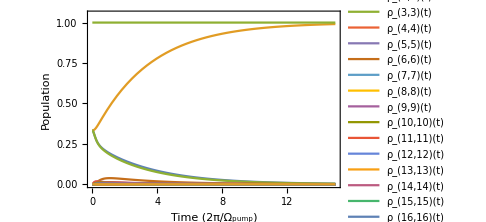

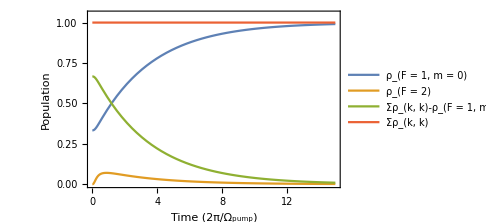

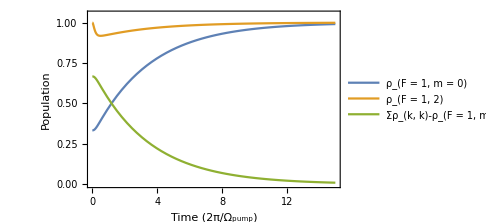

```mathematica
icEqs=Array[(rho/.t-> 0)[[#]]==rho0[[#]]&,Length[rho]];
{time,soln}= Timing[First@NDSolve[Flatten@Join[Eqs,icEqs], rho, {t,0,tmax},Method->Automatic]](*,MaxStepFraction->0.001]]*);
Print["Time to run sim: ",time];
labels=rho[[;;dim]];
AppendTo[labels,"Σρ_(k, k)"];
lines=Re[(rho/.soln)[[;;dim]]];
AppendTo[lines,Total[(rho/.soln)[[;;dim]]]];
(*Plot[Evaluate[lines], {t, 0,tmax },PlotRange->All,PlotLegends->labels]*)
Plot[Evaluate[lines/.t->τ (2π)/Ωeff], {τ, 0,tmax Ωeff/(2π)},PlotRange->{{0,tmax Ωeff/(2π)},{0,1.05}},PlotLegends->labels,FrameLabel->{"Time (2π/Ω_pump)","Population"}]
Plot[Evaluate[{lines[[2]],Total[lines[[4;;8]]],1-lines[[2]],lines[[-1]]}/.t->τ (2π)/Ωeff], {τ, 0,tmax Ωeff/(2π)},PlotRange->{{0,tmax Ωeff/(2π)},{0,1.05}},PlotLegends->{"ρ_(F = 1, m = 0)","ρ_(F = 2)","Σρ_(k, k)-ρ_(F = 1, m = 0)","Σρ_(k, k)"},FrameLabel->{"Time (2π/Ω_pump)","Population"}]
Plot[Evaluate[{lines[[2]],Total[lines[[1;;8]]],1-lines[[2]](*,lines[[-1]]*)}/.t->τ (2π)/Ωeff], {τ, 0,tmax Ωeff/(2π)},PlotLegends->{"ρ_(F = 1, m = 0)","ρ_(F = 1, 2)","Σρ_(k, k)-ρ_(F = 1, m = 0)","Σρ_(k, k)"},FrameLabel->{"Time (2π/Ω_pump)","Population"},PlotRange->{{0,tmax Ωeff/(2π)},{0,1.05}}]
```

Same plots as above, but time in microseconds.

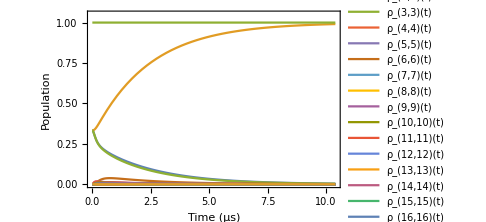

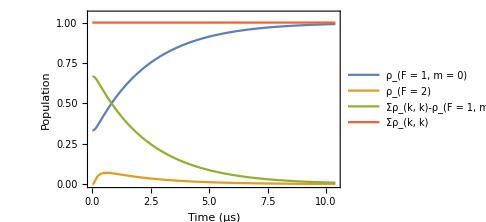

```mathematica
Plot[Evaluate[lines/.t->τ 1000], {τ, 0,tmax/1000},PlotRange->{{0,tmax/1000},{0,1.05}},PlotLegends->labels,FrameLabel->{"Time (μs)","Population"}]
Plot[Evaluate[{lines[[2]],Total[lines[[4;;8]]],1-lines[[2]],lines[[-1]]}/.t->τ 1000], {τ, 0,tmax/1000},PlotRange->{{0,tmax/1000},{0,1.05}},PlotLegends->{"ρ_(F = 1, m = 0)","ρ_(F = 2)","Σρ_(k, k)-ρ_(F = 1, m = 0)","Σρ_(k, k)"},FrameLabel->{"Time (μs)","Population"}]
```

## ^87 Rb - D1 optical pumping with D2 repump, rotated repump polarization

Optical pumping to the F=1,m=0 ground state. Linear pump light is resonant with F=1->F’=1, and linear repump light is resonant with F=2->F’=2

```mathematica
(*states with n,L,J,F,mF, and angular frequency (energy) in 2π*GHz wrt ground state C.o.M. energy*)

Fglist=Range[Abs[INuc-1/2],INuc+1/2];(*list of ground state hyperfine levels F*)
Fe1list=Range[Abs[INuc-1/2],INuc+1/2];
Fe2list=Range[Abs[INuc-3/2],INuc+3/2];
FivePThreeHalves=Flatten[Table[Table[{5,1,3/2,f,mf},{mf,Range[-f,f]}],{f,Fe2list}(*Range[Abs[INuc-3/2],INuc+3/2]}*)],1];
FivePOneHalf=Flatten[Table[Table[{5,1,1/2,f,mf},{mf,Range[-f,f]}],{f,Fe1list}],1];
FiveSOneHalf=Flatten[Table[Table[{5,0,1/2,f,mf},{mf,Range[-f,f]}],{f,Fglist}],1];
states=Join[FiveSOneHalf,FivePOneHalf,FivePThreeHalves];
{n,L,J,F,mF}=Transpose@states;
"Total number of states:"
dim=Length[states]

(*the energy of each state*)
ω=Table[2π Rb87fGHz[states[[i]][[;;4]]],{i,Range[dim]}];

(*lists of field amplitudes, ang. frequencies, polarization, and angle in rad*)
Clear[Εpump,Εrepump,γD1,γD2,dD1,dD2](*leave symbolic so it's easy to read the equations*);

det =2π*10^-10;(*detuning. must be finite, but can be arbitrarily small... where does the 1/0 come from?*)
Efields={{Εpump,2π(Rb87fGHz[{5,1,1/2,1}]-Rb87fGHz[{5,0,1/2,1}]-det),0,0},{Εrepump,2π(Rb87fGHz[{5,1,3/2,2}]-Rb87fGHz[{5,0,1/2,2}]-det),0,π/2}};
{Ep,ωp,q,θ}=Transpose@Efields;
dimE=Length[Ep];

(*--things that depend on a pair of state indices j and k--*)
E1FineReduced[j_,k_]:=Switch[Sort[{{n[[j]],L[[j]],J[[j]]},{n[[k]],L[[k]],J[[k]]}}],{{5,0,1/2},{5,1,1/2}},dD1,{{5,0,1/2},{5,1,3/2}},dD2,_,0];(*get hardcoded D1 or D2 line reduced dipole matrix element.*)

dRotated[m_,n_,p_]:=Module[{j,k},
{j,k}=Sort[{m,n}];(*because the matrix element is real, it is equal to its complex conjugate. Hence, d[m,n,p]=d[n,m,p].*)
Quiet[(Sum[WignerD[{F[[k]],mF[[k]],mFk},θ[[p]]]WignerD[{F[[j]],mFj,mF[[j]]},θ[[p]]]ClebschGordan[{F[[j]],mFj},{1,q[[p]]},{F[[k]],mFk}],{mFk,Range[-F[[k]],F[[k]]]},{mFj,Range[-F[[j]],F[[j]]]}])(-1)^(1+INuc+J[[k]]+F[[j]])√(2F[[j]]+1)SixJSymbol[{J[[j]],INuc,F[[j]]},{F[[k]],1,J[[k]]}]E1FineReduced[j,k]]
]

γE1[j_,k_]:=Switch[Sort[{{n[[j]],L[[j]],J[[j]]},{n[[k]],L[[k]],J[[k]]}}],{{5,0,1/2},{5,1,1/2}},γD1,{{5,0,1/2},{5,1,3/2}},γD2,_,0];(*get hardcoded D1 or D2 line natural linewidth.*)

(*branching factor from an upper state k to j*)
b[{J_,F_,mF_},{JJ_,FF_,mFF_}]:=Quiet[(2F+1)SixJSymbol[{J,INuc,F},{FF,1,JJ}]^2 ClebschGordan[{F,mF},{1,mFF-mF},{FF,mFF}]^2];

(*pre-evaluate b values*)
Table[Subscript[bb, J[[j]],F[[j]],mF[[j]],J[[k]],F[[k]],mF[[k]]]=b[{J[[j]],F[[j]],mF[[j]]},{J[[k]],F[[k]],mF[[k]]}],{j,Range[dim]},{k,Range[j,dim]}];

(*decay from state k to j*)
γ[j_,k_]:=γE1[j,k](Subscript[bb, J[[j]],F[[j]],mF[[j]],J[[k]],F[[k]],mF[[k]]]/Total[Flatten[Table[Subscript[bb, J[[1]],Fg,mFg,J[[k]],F[[k]],mF[[k]]],{Fg,Fglist},{mFg,Range[-Fg,Fg]}],1]]);
(*γ[j_,k_]:=γE1[j,k](b[{J[[j]],F[[j]],mF[[j]]},{J[[k]],F[[k]],mF[[k]]}]/Total[Flatten[Table[Table[b[{J[[1]],Fg,mFg},{J[[k]],F[[k]],mF[[k]]}],{mFg,Range[-Fg,Fg]}],{Fg,Fglist}]]]);*)

Δ[p_,k_,j_]:=ωp[[p]]-(ω[[k]]-ω[[j]]);

(*pre-evaluate γ, d, and Δ values which we can "look up" by index*)
Table[γlookup[j,k]=γ[j,k],{j,Range[dim]},{k,Range[j,dim]}];
Table[dlookup[j,k,p]=dRotated[j,k,p],{p,Range[dimE]},{j,Range[dim]},{k,Range[dim]}];
Table[Δlookup[p,k,j]=Δ[p,k,j],{p,Range[dimE]},{j,Range[dim]},{k,Range[dim]}];

(*terms with detunings of greater order of magnitude (GHz) than this will be dropped*)
drop=OoM[1]+1;(*GHz*)

(*coherence equations to exclude for an approximate but much faster result*)
gExclude=Flatten[Table[{k,j},{j,Range[8]},{k,Range[j+1,8]}],1];(*coherences betweeen  5S1/2 hyperfine states*)
eExclude=Flatten[Table[{k,j},{j,Range[9,30]},{k,Range[j+1,30]}],1];(*coherences betweeen  5P1/2 hyperfine states, 5P3/2 states, and between 5P1/2 and 5P3/2 states*)
exclude=Join[gExclude,eExclude];

Eqs = MEqs[states,Ep,Δlookup,dlookup,γlookup,drop,exclude];(*generate the differential equations*)
"Number of equations"
Eqs//Length
(*"The equations to be solved:"
For[i=1,i<Length[Eqs]+1,i++,
Print[Eqs[[i]]//Expand//TraditionalForm]
]*)
```

Total number of states:

32

Number of equations

269

```mathematica
(*--define numerical constants--*)
dD1=D1MatElem;
dD2=D2MatElem;
γD1=ΓD1*10^-9;
γD2=ΓD2*10^-9;
Εpump=√(2/(c ϵ0)IsatD1SI) /GHz;
Εrepump=100√(2/(c ϵ0)IsatD2SI) /GHz;

(*--setup for the numerical solver--*)

(*the list of populations and coherences we're including, in the same order as in Eqs*)
rho=Join[Table[Subscript[ρ, k,k][t],{k,Range[dim]}],Complement[Flatten[Table[Subscript[ρ, k,l][t],{l,1,dim},{k,l+1,dim}],1],Array[Subscript[ρ, exclude[[#,1]],exclude[[#,2]]][t]&,Length[exclude]]]];
rho0=Array[0&,Length[rho]];
initialStates=Range[3];
rho0[[initialStates]]=1/(initialStates//Length);
Ωpump=Εpump dRotated[1,9,1]/ℏ;
Ωrepump=Εpump dRotated[4,21,1]/ℏ;
Ωeff=Abs[Ωpump] ;
Print["Pump Rabi frequency = 2π*",Abs[Ωpump]/(2π) GHz/MHz," MHz"]
Print["Repump Rabi frequency = 2π*",Abs[Ωrepump]/(2π) GHz/MHz," MHz"]
Print["Ω_pump/γD1 = ",Abs[Ωpump]/γD1]
Print["Ω_repump/γD2 = ",Abs[Ωrepump]/γD2]
tmax=15*2π/Ωeff;
```

Pump Rabi frequency = 2π*1.44304 MHz

Repump Rabi frequency = 2π*2.88298 MHz

Ω_pump/γD1 = 0.251104

Ω_repump/γD2 = 0.475277

Time to run sim: 33.625

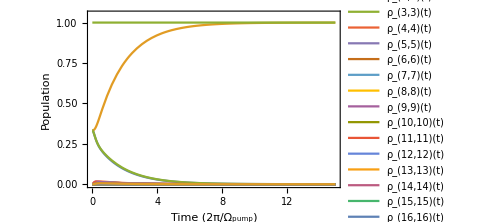

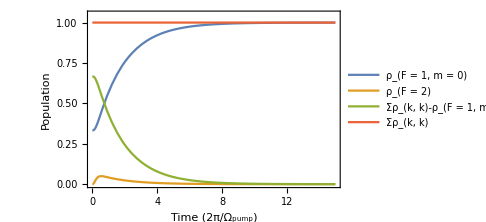

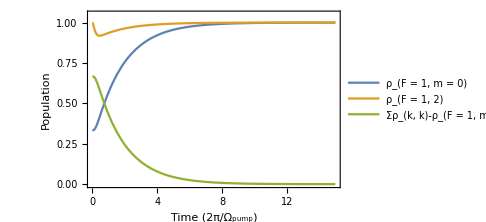

```mathematica
icEqs=Array[(rho/.t-> 0)[[#]]==rho0[[#]]&,Length[rho]];
{time,soln}= Timing[First@NDSolve[Flatten@Join[Eqs,icEqs], rho, {t,0,tmax},Method->Automatic]](*,MaxStepFraction->0.001]]*);
Print["Time to run sim: ",time];
labels=rho[[;;dim]];
AppendTo[labels,"Σρ_(k, k)"];
lines=Re[(rho/.soln)[[;;dim]]];
AppendTo[lines,Total[(rho/.soln)[[;;dim]]]];
(*Plot[Evaluate[lines], {t, 0,tmax },PlotRange->All,PlotLegends->labels]*)
Plot[Evaluate[lines/.t->τ (2π)/Ωeff], {τ, 0,tmax Ωeff/(2π)},PlotRange->{{0,tmax Ωeff/(2π)},{0,1.05}},PlotLegends->labels,FrameLabel->{"Time (2π/Ω_pump)","Population"}]
Plot[Evaluate[{lines[[2]],Total[lines[[4;;8]]],1-lines[[2]],lines[[-1]]}/.t->τ (2π)/Ωeff], {τ, 0,tmax Ωeff/(2π)},PlotRange->{{0,tmax Ωeff/(2π)},{0,1.05}},PlotLegends->{"ρ_(F = 1, m = 0)","ρ_(F = 2)","Σρ_(k, k)-ρ_(F = 1, m = 0)","Σρ_(k, k)"},FrameLabel->{"Time (2π/Ω_pump)","Population"}]
Plot[Evaluate[{lines[[2]],Total[lines[[1;;8]]],1-lines[[2]](*,lines[[-1]]*)}/.t->τ (2π)/Ωeff], {τ, 0,tmax Ωeff/(2π)},PlotLegends->{"ρ_(F = 1, m = 0)","ρ_(F = 1, 2)","Σρ_(k, k)-ρ_(F = 1, m = 0)","Σρ_(k, k)"},FrameLabel->{"Time (2π/Ω_pump)","Population"},PlotRange->{{0,tmax Ωeff/(2π)},{0,1.05}}]
```

Same plots as above, but time in microseconds.

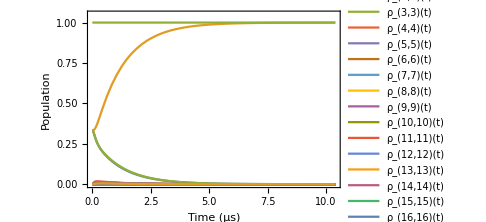

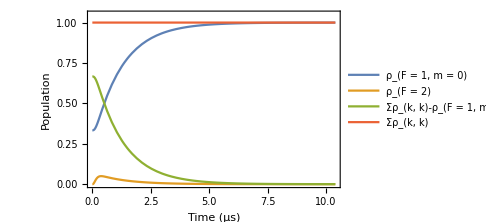

```mathematica
Plot[Evaluate[lines/.t->τ 1000], {τ, 0,tmax/1000},PlotRange->{{0,tmax/1000},{0,1.05}},PlotLegends->labels,FrameLabel->{"Time (μs)","Population"}]
Plot[Evaluate[{lines[[2]],Total[lines[[4;;8]]],1-lines[[2]],lines[[-1]]}/.t->τ 1000], {τ, 0,tmax/1000},PlotRange->{{0,tmax/1000},{0,1.05}},PlotLegends->{"ρ_(F = 1, m = 0)","ρ_(F = 2)","Σρ_(k, k)-ρ_(F = 1, m = 0)","Σρ_(k, k)"},FrameLabel->{"Time (μs)","Population"}]
```

## misc. testing

Simulations in this section may not be correct, as this section is used for trying to reproduce bugs and test code.

```mathematica
f[x_,y_:2]:=x^2+y^2;
```

```mathematica
f[2]
```

8

## rotated dipole operator

```mathematica
d[m_,n_,p_]:=Module[{j,k},
{j,k}=Sort[{m,n}];(*because the matrix element is real, it is equal to its complex conjugate. Hence, when the state labels are reversed the value return is the same.*)
Quiet[(-1)^(1+INuc+J[[k]]+F[[j]])√(2F[[j]]+1)SixJSymbol[{J[[j]],INuc,F[[j]]},{F[[k]],1,J[[k]]}]ClebschGordan[{F[[j]],mF[[j]]},{1,q[[p]]},{F[[k]],mF[[k]]}]E1FineReduced[j,k]]
](*the hyperfine dipole matrix element.TODO: make general by including the Wigner D to allow rotations*)
```

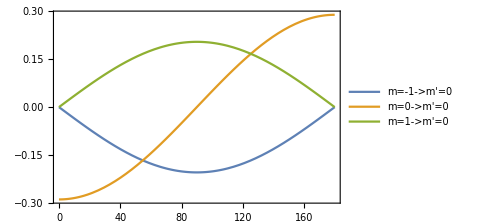

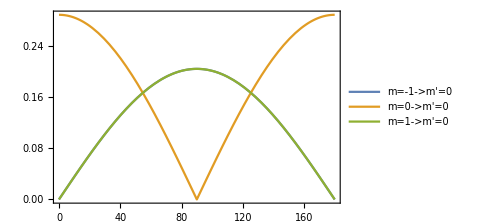

```mathematica
states={{5,0,1/2,1,-1},{5,0,1/2,1,0},{5,0,1/2,1,1},{5,1,3/2,0,0}};
{n,L,J,F,mF}=Transpose@states;
Efields={{0,β}};
{q,θ}=Transpose@Efields;

d[m_,n_,p_]:=Module[{j,k},
{j,k}=Sort[{m,n}];(*because the matrix element is real, it is equal to its complex conjugate. Hence, when the state labels are reversed the value return is the same.*)
Quiet[(-1)^(1+INuc+J[[k]]+F[[j]])√(2F[[j]]+1)SixJSymbol[{J[[j]],INuc,F[[j]]},{F[[k]],1,J[[k]]}]ClebschGordan[{F[[j]],mF[[j]]},{1,q[[p]]},{F[[k]],mF[[k]]}]E1FineReduced[j,k]]
]

dRotated[m_,n_,p_]:=Module[{j,k},
{j,k}=Sort[{m,n}];(*because the matrix element is real, it is equal to its complex conjugate. Hence, when the state labels are reversed the value return is the same.*)
Quiet[(Sum[WignerD[{F[[k]],mF[[k]],mFk},θ[[p]]]WignerD[{F[[j]],mFj,mF[[j]]},θ[[p]]]ClebschGordan[{F[[j]],mFj},{1,q[[p]]},{F[[k]],mFk}],{mFk,Range[-F[[k]],F[[k]]]},{mFj,Range[-F[[j]],F[[j]]]}])(-1)^(1+INuc+J[[k]]+F[[j]])√(2F[[j]]+1)SixJSymbol[{J[[j]],INuc,F[[j]]},{F[[k]],1,J[[k]]}](*E1FineReduced[j,k]*)]
]

Plot[Evaluate[Table[dRotated[j,4,1]/.β->deg π/180,{j,Range[3]}]],{deg,0,180},PlotLegends->{"m=-1->m'=0","m=0->m'=0","m=1->m'=0"}]
Plot[Evaluate[Table[Abs[dRotated[j,4,1]/.β->deg π/180],{j,Range[3]}]],{deg,0,180},PlotLegends->{"m=-1->m'=0","m=0->m'=0","m=1->m'=0"}]
```

## ^87 Rb - D1 line

D1 debugging. Only using F=1,F’=1 states unless otherwise stated.
* population starting evenly distributed among F’=1 and no driving: the population decays to F=1 until the population is evenly distributed. good.
* population starting evenly distributed among F=1 with resonant driving with linear or σ+ light does not transfer any of the population out of the ground state. I have checked that the field is indeed resonant with the states. the coherence terms eventually start to blow up; this could be numerical error. I have tried fields proportional to 0.1, 1, and 10 √I_sat. equations appear correct upon inspection, including the driving terms.
* isolate the system to only the cycling transition F=1->F’=2.

```mathematica
Clear[MEqs]
MEqs[stateList_,fieldAmplitudes_,detunings_,dipoleMatrixElement_,decayRate_,dropFastOoM_,excludeIndices_]:=Module[{drop,states=stateList,Ep=fieldAmplitudes,d=dipoleMatrixElement,γ=decayRate,Δ=detunings,l=1,k=1,dim=1,dimE=1,populationRHS, coherenceRHS,populationDriving,populationDecay,coherenceDriving,coherenceDecay,RHS=0,Eqs={},HO,Ex},
(*Builds the density matrix master equation in Linblad form for each element Subscript[ρ, k,l] with k>l and k increasing in order of energy. The coherence terms are actually ρ̃=ρⅇ^-ⅈωt.

--- Params ---
fieldAmplitudes, detunings, dipoleMatrixElement, and decayRate: functions that depend on state indices j,k and field indices p to return the appropriate quantity. See usage below.

dropFastOoM: an order of magnitude of the detuning (in the chosen energy units of the states and fields, e.g. GHz).

excludeIndices: a list of indices {k,l} for which equations for Subscript[ρ, k,l] and dependence on Subscript[ρ, k,l] in other eqs will be dropped
*)
dim = Length[states];
dimE=Length[Ep];
(*--multipliers for systematically dropping terms--*)
Table[Subscript[HO, p,i,j]=DropHiOsc[Δ[p,i,j],dropFastOoM],{p,Range[dimE]},{i,Range[dim]},{j,Range[dim]}];(*for removing highly oscillatory (far off-resonant) terms*)
Table[Subscript[Ex, k,l]=Subscript[Ex, l,k]=Boole[!MemberQ[excludeIndices,{k,l}]],{l,Range[dim]},{k,Range[l,dim]}];(*for removing the equations for and terms with Subscript[ρ, k,l] if {k,l} ∈ excludeIndices*)

(*--Generate the population eqs--*)
For[k=1,k<dim+1,k++,
RHS=
-Sum[γ[j,k]Subscript[ρ, k,k][t],{j,Range[1,k-1]}]+Sum[γ[k,j]Subscript[ρ, j,j][t],{j,Range[k+1,dim]}]
-ⅈ/(2ℏ)(Sum[(-Ep[[p]]d[k,j,p]Subscript[ρ, k,j][t]*Exp[-ⅈ Δ[p,k,j]t]+Ep[[p]]*d[j,k,p]Subscript[ρ, k,j][t]Exp[ⅈ Δ[p,k,j]t])Subscript[HO, p,k,j] Subscript[Ex, k,j],{p,Range[dimE]},{j,Range[1,k-1]}]
+Sum[(Ep[[p]]d[j,k,p]Subscript[ρ, j,k][t]*Exp[-ⅈ Δ[p,j,k]t]-Ep[[p]]*d[k,j,p]Subscript[ρ, j,k][t]Exp[ⅈ Δ[p,j,k]t])Subscript[HO, p,j,k] Subscript[Ex, j,k],{p,Range[dimE]},{j,Range[k+1,dim]}]);
AppendTo[Eqs,D[Subscript[ρ, k,k][t],t]==RHS];
];
(*--Generate the coherence eqs--*)
For[l=1,l<dim+1,l++,
For[k=l+1,k<dim+1,k++,
If[!MemberQ[excludeIndices,{k,l}],
RHS=1/2(-(Sum[γ[j,k],{j,Range[1,k-1]}]+Sum[γ[j,l],{j,Range[1,l-1]}])Subscript[ρ, k,l][t]
+Sum[γ[k,j]Subscript[ρ, j,l][t](1-δ[j,l])Subscript[Ex, j,l],{j,Range[k+1,dim]}]+Sum[γ[l,j]Subscript[ρ, k,j][t](1-δ[k,j])Subscript[Ex, k,j],{j,Range[l+1,k-1]}]+Sum[γ[l,j]Subscript[ρ, j,k][t]*(1-δ[k,j])Subscript[Ex, j,k],{j,Range[k+1,dim]}]
-ⅈ/ℏ(Sum[-Ep[[p]]d[k,j,p]Subscript[ρ, l,j][t]*Exp[-ⅈ Δ[p,k,j]t] Subscript[HO, p,k,j] Subscript[Ex, l,j]+Ep[[p]]*d[j,l,p]Subscript[ρ, k,j][t]Exp[ⅈ Δ[p,l,j]t] Subscript[HO, p,l,j] Subscript[Ex, k,j],{p,Range[dimE]},{j,Range[1,l-1]}]
+Sum[Ep[[p]](d[j,l,p]Subscript[ρ, k,j][t]Exp[-ⅈ Δ[p,j,l]t] Subscript[HO, p,j,l] Subscript[Ex, k,j]-d[k,j,p]Subscript[ρ, j,l][t]Exp[-ⅈ Δ[p,k,j]t] Subscript[HO, p,k,j] Subscript[Ex, j,l]),{p,Range[dimE]},{j,Range[l,k-1]}]
+Sum[Ep[[p]]d[j,l,p]Subscript[ρ, j,k][t]*Exp[-ⅈ Δ[p,j,l]t] Subscript[HO, p,j,l] Subscript[Ex, j,k]-Ep[[p]]*d[k,j,p]Subscript[ρ, j,l][t]Exp[ⅈ Δ[p,j,k]t] Subscript[HO, p,j,k] Subscript[Ex, j,l],{p,Range[dimE]},{j,Range[k,dim]}]));
AppendTo[Eqs,D[Subscript[ρ, k,l][t],t]==RHS];
];
];
];

Eqs
]
```

## F=1->F’=1

```mathematica
(*states with n,L,J,F,mF, and angular frequency (energy) in 2π*GHz wrt ground state C.o.M. energy*)

Fglist={1}(*Range[Abs[INuc-1/2],INuc+1/2]*);(*list of ground state hyperfine levels F*)
Fe1list=Fglist(*Range[Abs[INuc-1/2],INuc+1/2]*);
Fe2list={2};(*Range[Abs[INuc-3/2],INuc+3/2]*);
FivePThreeHalves=Flatten[Table[Table[{5,1,3/2,f,mf},{mf,Range[-f,f]}],{f,Fe2list}(*Range[Abs[INuc-3/2],INuc+3/2]}*)],1];
FivePOneHalf=Flatten[Table[Table[{5,1,1/2,f,mf},{mf,Range[-f,f]}],{f,Fe1list}],1];
FiveSOneHalf=Flatten[Table[Table[{5,0,1/2,f,mf},{mf,Range[-f,f]}],{f,Fglist}],1];
states=Join[FiveSOneHalf,FivePOneHalf(*,FivePThreeHalves*)];
{n,L,J,F,mF}=Transpose@states;
"Total number of states:"
dim=Length[states]

(*the energy of each state*)
ω=Table[2π Rb87fGHz[states[[i]][[;;4]]],{i,Range[dim]}];

(*lists of field amplitudes, ang. frequencies, polarization, and angle in rad*)
Clear[Ε1,Ε2,γD1,γD2,dD1,dD2](*leave symbolic so it's easy to read the equations*);

(*--define numerical constants--*)
dD1=D1MatElem;
dD2=D2MatElem;
γD1=ΓD1*10^-9;
γD2=ΓD2*10^-9;
Ε1=Ε2=.1√(2/(c ϵ0)IsatD1SI) /GHz;

det =2π*10^-9;(*detuning. must be finite, but can be arbitrarily small... where does the 1/0 come from?*)
Efields={{Ε1,2π(Rb87fGHz[{5,1,1/2,1}]-Rb87fGHz[{5,0,1/2,1}]-det),0,0}(*,{Ε2,2π(Rb87fGHz[{5,1,3/2,2}]-Rb87fGHz[{5,0,1/2,2}])-det, 0,0}*)};
{Ep,ωp,q,θ}=Transpose@Efields;
dimE=Length[Ep];

(*--things that depend on a pair of state indices j and k--*)
E1FineReduced[j_,k_]:=Switch[Sort[{{n[[j]],L[[j]],J[[j]]},{n[[k]],L[[k]],J[[k]]}}],{{5,0,1/2},{5,1,1/2}},dD1,{{5,0,1/2},{5,1,3/2}},dD2,_,0];(*get hardcoded D1 or D2 line reduced dipole matrix element.*)

d[m_,n_,p_]:=Module[{j,k},
{j,k}=Sort[{m,n}];(*because the matrix element is real, it is equal to its complex conjugate. Hence, when the state labels are reversed the value return is the same.*)
Quiet[(-1)^(1+INuc+J[[k]]+F[[j]])√(2F[[j]]+1)SixJSymbol[{J[[j]],INuc,F[[j]]},{F[[k]],1,J[[k]]}]ClebschGordan[{F[[j]],mF[[j]]},{1,q[[p]]},{F[[k]],mF[[k]]}]E1FineReduced[j,k]]
](*the hyperfine dipole matrix element.TODO: make general by including the Wigner D to allow rotations*)

γE1[j_,k_]:=Switch[Sort[{{n[[j]],L[[j]],J[[j]]},{n[[k]],L[[k]],J[[k]]}}],{{5,0,1/2},{5,1,1/2}},γD1,{{5,0,1/2},{5,1,3/2}},γD2,_,0];(*get hardcoded D1 or D2 line natural linewidth.*)

(*branching factor from an upper state k to j*)
b[{J_,F_,mF_},{JJ_,FF_,mFF_}]:=Quiet[(2F+1)SixJSymbol[{J,INuc,F},{FF,1,JJ}]^2 ClebschGordan[{F,mF},{1,mFF-mF},{FF,mFF}]^2];

(*pre-evaluate b values*)
Table[Subscript[bb, J[[j]],F[[j]],mF[[j]],J[[k]],F[[k]],mF[[k]]]=b[{J[[j]],F[[j]],mF[[j]]},{J[[k]],F[[k]],mF[[k]]}],{j,Range[dim]},{k,Range[j,dim]}];

(*decay from state k to j*)
γ[j_,k_]:=γE1[j,k](Subscript[bb, J[[j]],F[[j]],mF[[j]],J[[k]],F[[k]],mF[[k]]]/Total[Flatten[Table[Subscript[bb, J[[1]],Fg,mFg,J[[k]],F[[k]],mF[[k]]],{Fg,Fglist},{mFg,Range[-Fg,Fg]}],1]]);
(*γ[j_,k_]:=γE1[j,k](b[{J[[j]],F[[j]],mF[[j]]},{J[[k]],F[[k]],mF[[k]]}]/Total[Flatten[Table[Table[b[{J[[1]],Fg,mFg},{J[[k]],F[[k]],mF[[k]]}],{mFg,Range[-Fg,Fg]}],{Fg,Fglist}]]]);*)

Δ[p_,k_,j_]:=ωp[[p]]-(ω[[k]]-ω[[j]]);

(*pre-evaluate γ, d, and Δ values which we can "look up" by index*)
Table[γlookup[j,k]=γ[j,k],{j,Range[dim]},{k,Range[j,dim]}];
Table[dlookup[j,k,p]=d[j,k,p],{p,Range[dimE]},{j,Range[dim]},{k,Range[dim]}];
Table[Δlookup[p,k,j]=Δ[p,k,j],{p,Range[dimE]},{j,Range[dim]},{k,Range[dim]}];

(*terms with detunings of greater order of magnitude (GHz) than this will be dropped*)
drop=OoM[10]+1;(*GHz*)

(*equations to exclude for an approximate but much faster result*)
gExclude=Flatten[Table[{k,j},{j,Range[3]},{k,Range[j+1,3]}],1];(*coherences betweeen  5S1/2 hyperfine states*)
eExclude=Flatten[Table[{k,j},{j,Range[4,6]},{k,Range[j+1,6]}],1];(*coherences betweeen  5P1/2 hyperfine states*)
exclude=Join[gExclude,eExclude];

Eqs = MEqs[states,Ep,Δlookup,dlookup,γlookup,drop,exclude];(*generate the differential equations*)
"Number of equations"
Eqs//Length
"The equations to be solved:"
For[i=1,i<Length[Eqs]+1,i++,
Print[Eqs[[i]]//Expand//TraditionalForm]
]
```

Total number of states:

6

Number of equations

15

The equations to be solved:

ρ_(1,1)'(t)==(0.-0.000453346 ⅈ) ⅇ^((0.+4.00469×10^-8 ⅈ) t) Conjugate[ρ_(4,1)(t)]+(0.+0.000453346 ⅈ) ⅇ^((0.-4.00469×10^-8 ⅈ) t) ρ_(4,1)(t)+0.0180541 ρ_(4,4)(t)+0.0180541 ρ_(5,5)(t)+(0.+0. ⅈ)

ρ_(2,2)'(t)==0.0180541 ρ_(4,4)(t)+0.0180541 ρ_(6,6)(t)+(0.+0. ⅈ)

ρ_(3,3)'(t)==(0.+0.000453346 ⅈ) ⅇ^((0.+4.00469×10^-8 ⅈ) t) Conjugate[ρ_(6,3)(t)]-(0.+0.000453346 ⅈ) ⅇ^((0.-4.00469×10^-8 ⅈ) t) ρ_(6,3)(t)+0.0180541 ρ_(5,5)(t)+0.0180541 ρ_(6,6)(t)+(0.+0. ⅈ)

ρ_(4,4)'(t)==(0.+0.000453346 ⅈ) ⅇ^((0.+4.00469×10^-8 ⅈ) t) Conjugate[ρ_(4,1)(t)]-(0.+0.000453346 ⅈ) ⅇ^((0.-4.00469×10^-8 ⅈ) t) ρ_(4,1)(t)-0.0361082 ρ_(4,4)(t)+(0.+0. ⅈ)

ρ_(5,5)'(t)==-0.0361082 ρ_(5,5)(t)+(0.+0. ⅈ)

ρ_(6,6)'(t)==(0.-0.000453346 ⅈ) ⅇ^((0.+4.00469×10^-8 ⅈ) t) Conjugate[ρ_(6,3)(t)]+(0.+0.000453346 ⅈ) ⅇ^((0.-4.00469×10^-8 ⅈ) t) ρ_(6,3)(t)-0.0361082 ρ_(6,6)(t)+(0.+0. ⅈ)

ρ_(4,1)'(t)==(0.-0.000453346 ⅈ) ⅇ^((0.+4.00469×10^-8 ⅈ) t) Conjugate[ρ_(4,4)(t)]+(0.+0.000453346 ⅈ) ⅇ^((0.+4.00469×10^-8 ⅈ) t) ρ_(1,1)(t)-0.0180541 ρ_(4,1)(t)+(0.+0. ⅈ)

ρ_(5,1)'(t)==-0.0180541 ρ_(5,1)(t)+(0.+0. ⅈ)

ρ_(6,1)'(t)==-0.0180541 ρ_(6,1)(t)+(0.+0. ⅈ)

ρ_(4,2)'(t)==-0.0180541 ρ_(4,2)(t)+(0.+0. ⅈ)

ρ_(5,2)'(t)==-0.0180541 ρ_(5,2)(t)+(0.+0. ⅈ)

ρ_(6,2)'(t)==-0.0180541 ρ_(6,2)(t)+(0.+0. ⅈ)

ρ_(4,3)'(t)==-0.0180541 ρ_(4,3)(t)+(0.+0. ⅈ)

ρ_(5,3)'(t)==-0.0180541 ρ_(5,3)(t)+(0.+0. ⅈ)

ρ_(6,3)'(t)==(0.+0.000453346 ⅈ) ⅇ^((0.+4.00469×10^-8 ⅈ) t) Conjugate[ρ_(6,6)(t)]-(0.+0.000453346 ⅈ) ⅇ^((0.+4.00469×10^-8 ⅈ) t) ρ_(3,3)(t)-0.0180541 ρ_(6,3)(t)+(0.+0. ⅈ)

```mathematica
(*--setup for the numerical solver--*)

(*the list of populations and coherences we're including, in the same order as in Eqs*)
rho=Join[Table[Subscript[ρ, k,k][t],{k,Range[dim]}],Complement[Flatten[Table[Subscript[ρ, k,l][t],{l,1,dim},{k,l+1,dim}],1],Array[Subscript[ρ, exclude[[#,1]],exclude[[#,2]]][t]&,Length[exclude]]]];
rho0=Array[0&,Length[rho]];
rho0[[{1,2,3}]]=1/3;
Ω1=Ε1 d[1,4,1]/ℏ;
(*Ω2=Ε2 d[8,17,2]/ℏ;*)
Ωeff=Abs[Ω1] ;
Print["Effective rabi frequency = 2π*",Ωeff GHz/10^6," MHz"]
tmax=100*2π/Ωeff;
```

Effective rabi frequency = 2π*0.906691 MHz

Time to run sim: 0.03125

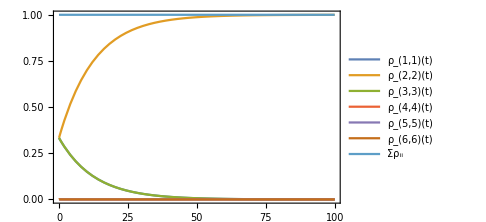

```mathematica
icEqs=Array[(rho/.t-> 0)[[#]]==rho0[[#]]&,Length[rho]];
{time,soln}= Timing[First@NDSolve[Flatten@Join[Eqs,icEqs], rho, {t,0,tmax},Method->Automatic]](*,MaxStepFraction->0.001]]*);
Print["Time to run sim: ",time];
labels=rho[[;;dim]];
AppendTo[labels,Subscript[Σρ, ii]];
lines=Re[(rho/.soln)[[;;dim]]];
AppendTo[lines,Total[(rho/.soln)[[;;dim]]]];
(*Plot[Evaluate[lines], {t, 0,tmax },PlotRange->All,PlotLegends->labels]*)
Plot[Evaluate[lines/.t->τ (2π)/Ωeff], {τ, 0,tmax Ωeff/(2π)},PlotRange->All,PlotLegends->labels]
```

## F=1->F’=2

```mathematica
(*states with n,L,J,F,mF, and angular frequency (energy) in 2π*GHz wrt ground state C.o.M. energy*)

Fglist={1}(*Range[Abs[INuc-1/2],INuc+1/2]*);(*list of ground state hyperfine levels F*)
Fe1list={2}(*Range[Abs[INuc-1/2],INuc+1/2]*);
Fe2list={2};(*Range[Abs[INuc-3/2],INuc+3/2]*);
FivePThreeHalves=Flatten[Table[Table[{5,1,3/2,f,mf},{mf,Range[-f,f]}],{f,Fe2list}(*Range[Abs[INuc-3/2],INuc+3/2]}*)],1];
FivePOneHalf=Flatten[Table[Table[{5,1,1/2,f,mf},{mf,Range[-f,f]}],{f,Fe1list}],1];
FiveSOneHalf=Flatten[Table[Table[{5,0,1/2,f,mf},{mf,Range[-f,f]}],{f,Fglist}],1];
states=Join[FiveSOneHalf,FivePOneHalf(*,FivePThreeHalves*)];
{n,L,J,F,mF}=Transpose@states;
"Total number of states:"
dim=Length[states]

(*the energy of each state*)
ω=Array[2π Rb87fGHz[states[[#]][[;;4]]]&,dim];

(*lists of field amplitudes, ang. frequencies, polarization, and angle in rad*)
Clear[Ε1,Ε2,γD1,γD2,dD1,dD2](*leave symbolic so it's easy to read the equations*);

(*--define numerical constants--*)
(*dD1=D1MatElem;
dD2=D2MatElem;
γD1=ΓD1*10^-9;
γD2=ΓD2*10^-9;
Ε1=Ε2=10√(2/(c ϵ0)IsatD1SI) /GHz;*)

det =2π*10^-9;(*detuning. must be finite, but can be arbitrarily small... where does the 1/0 come from?*)
Efields={{Ε1,2π(Rb87fGHz[{5,1,1/2,2}]-Rb87fGHz[{5,0,1/2,1}]-det),1,0}(*,{Ε2,2π(Rb87fGHz[{5,1,3/2,2}]-Rb87fGHz[{5,0,1/2,2}])-det, 0,0}*)};
{Ep,ωp,q,θ}=Transpose@Efields;
dimE=Length[Ep];

(*--things that depend on a pair of state indices j and k--*)
E1FineReduced[j_,k_]:=Switch[Sort[{{n[[j]],L[[j]],J[[j]]},{n[[k]],L[[k]],J[[k]]}}],{{5,0,1/2},{5,1,1/2}},dD1,{{5,0,1/2},{5,1,3/2}},dD2,_,0];(*get hardcoded D1 or D2 line reduced dipole matrix element.*)

d[m_,n_,p_]:=Module[{j,k},
{j,k}=Sort[{m,n}];(*because the matrix element is real, it is equal to its complex conjugate. Hence, when the state labels are reversed the value return is the same.*)
Quiet[(-1)^(1+INuc+J[[k]]+F[[j]])√(2F[[j]]+1)SixJSymbol[{J[[j]],INuc,F[[j]]},{F[[k]],1,J[[k]]}]ClebschGordan[{F[[j]],mF[[j]]},{1,q[[p]]},{F[[k]],mF[[k]]}]E1FineReduced[j,k]]
](*the hyperfine dipole matrix element.TODO: make general by including the Wigner D to allow rotations*)(*the hyperfine dipole matrix element; the If takes care of the Hermitian conjugate. TODO: make general by including the Wigner D to allow rotations*)

γE1[j_,k_]:=Switch[Sort[{{n[[j]],L[[j]],J[[j]]},{n[[k]],L[[k]],J[[k]]}}],{{5,0,1/2},{5,1,1/2}},γD1,{{5,0,1/2},{5,1,3/2}},γD2,_,0];(*get hardcoded D1 or D2 line natural linewidth.*)

(*branching factor from an upper state k to j*)
b[{J_,F_,mF_},{JJ_,FF_,mFF_}]:=Quiet[(2F+1)SixJSymbol[{J,INuc,F},{FF,1,JJ}]^2 ClebschGordan[{F,mF},{1,mFF-mF},{FF,mFF}]^2];

(*pre-evaluate b values*)
Table[Subscript[bb, J[[j]],F[[j]],mF[[j]],J[[k]],F[[k]],mF[[k]]]=b[{J[[j]],F[[j]],mF[[j]]},{J[[k]],F[[k]],mF[[k]]}],{j,Range[dim]},{k,Range[j,dim]}];

(*decay from state k to j*)
γ[j_,k_]:=γE1[j,k](Subscript[bb, J[[j]],F[[j]],mF[[j]],J[[k]],F[[k]],mF[[k]]]/Total[Flatten[Table[Subscript[bb, J[[1]],Fg,mFg,J[[k]],F[[k]],mF[[k]]],{Fg,Fglist},{mFg,Range[-Fg,Fg]}],1]]);
(*γ[j_,k_]:=γE1[j,k](b[{J[[j]],F[[j]],mF[[j]]},{J[[k]],F[[k]],mF[[k]]}]/Total[Flatten[Table[Table[b[{J[[1]],Fg,mFg},{J[[k]],F[[k]],mF[[k]]}],{mFg,Range[-Fg,Fg]}],{Fg,Fglist}]]]);*)

Δ[p_,k_,j_]:=ωp[[p]]-(ω[[k]]-ω[[j]]);

(*pre-evaluate γ, d, and Δ values which we can "look up" by index*)
Table[γlookup[j,k]=γ[j,k],{j,Range[dim]},{k,Range[j,dim]}];
Table[dlookup[j,k,p]=d[j,k,p],{p,Range[dimE]},{j,Range[dim]},{k,Range[dim]}];
Table[Δlookup[p,k,j]=Δ[p,k,j],{p,Range[dimE]},{j,Range[dim]},{k,Range[dim]}];

(*terms with detunings of greater order of magnitude (GHz) than this will be dropped*)
drop=OoM[10]+1;(*GHz*)

(*equations to exclude for an approximate but much faster result*)
gExclude=Flatten[Table[{k,j},{j,Range[3]},{k,Range[j+1,3]}],1];(*coherences betweeen  5S1/2 hyperfine states*)
eExclude=Flatten[Table[{k,j},{j,Range[4,8]},{k,Range[j+1,8]}],1];(*coherences betweeen  5P1/2 hyperfine states*)
exclude=Join[gExclude,eExclude];

Eqs = MEqs[states,Ep,Δlookup,dlookup,γlookup,drop,exclude];(*generate the differential equations*)
"Number of equations"
Eqs//Length
"The equations to be solved:"
For[i=1,i<Length[Eqs]+1,i++,
Print[Eqs[[i]]//Expand//TraditionalForm]
]
```

Total number of states:

8

Number of equations

23

The equations to be solved:

ρ_(1,1)'(t)==(0.-9.7202×10^32 ⅈ) dD1 Ε1 ⅇ^((0.+3.95812×10^-8 ⅈ) t) Conjugate[ρ_(6,1)(t)]-(0.+9.7202×10^32 ⅈ) dD1 ⅇ^((0.-3.95812×10^-8 ⅈ) t) Conjugate[Ε1] ρ_(6,1)(t)+γD1 ρ_(4,4)(t)+1/2 γD1 ρ_(5,5)(t)+1/6 γD1 ρ_(6,6)(t)

ρ_(2,2)'(t)==(0.-1.68359×10^33 ⅈ) dD1 Ε1 ⅇ^((0.+3.95812×10^-8 ⅈ) t) Conjugate[ρ_(7,2)(t)]-(0.+1.68359×10^33 ⅈ) dD1 ⅇ^((0.-3.95812×10^-8 ⅈ) t) Conjugate[Ε1] ρ_(7,2)(t)+1/2 γD1 ρ_(5,5)(t)+2/3 γD1 ρ_(6,6)(t)+1/2 γD1 ρ_(7,7)(t)

ρ_(3,3)'(t)==(0.-2.38095×10^33 ⅈ) dD1 Ε1 ⅇ^((0.+3.95812×10^-8 ⅈ) t) Conjugate[ρ_(8,3)(t)]-(0.+2.38095×10^33 ⅈ) dD1 ⅇ^((0.-3.95812×10^-8 ⅈ) t) Conjugate[Ε1] ρ_(8,3)(t)+1/6 γD1 ρ_(6,6)(t)+1/2 γD1 ρ_(7,7)(t)+γD1 ρ_(8,8)(t)

ρ_(4,4)'(t)==-γD1 ρ_(4,4)(t)+(0.+0. ⅈ)

ρ_(5,5)'(t)==-γD1 ρ_(5,5)(t)+(0.+0. ⅈ)

ρ_(6,6)'(t)==(0.+9.7202×10^32 ⅈ) dD1 Ε1 ⅇ^((0.+3.95812×10^-8 ⅈ) t) Conjugate[ρ_(6,1)(t)]+(0.+9.7202×10^32 ⅈ) dD1 ⅇ^((0.-3.95812×10^-8 ⅈ) t) Conjugate[Ε1] ρ_(6,1)(t)-γD1 ρ_(6,6)(t)

ρ_(7,7)'(t)==(0.+1.68359×10^33 ⅈ) dD1 Ε1 ⅇ^((0.+3.95812×10^-8 ⅈ) t) Conjugate[ρ_(7,2)(t)]+(0.+1.68359×10^33 ⅈ) dD1 ⅇ^((0.-3.95812×10^-8 ⅈ) t) Conjugate[Ε1] ρ_(7,2)(t)-γD1 ρ_(7,7)(t)

ρ_(8,8)'(t)==(0.+2.38095×10^33 ⅈ) dD1 Ε1 ⅇ^((0.+3.95812×10^-8 ⅈ) t) Conjugate[ρ_(8,3)(t)]+(0.+2.38095×10^33 ⅈ) dD1 ⅇ^((0.-3.95812×10^-8 ⅈ) t) Conjugate[Ε1] ρ_(8,3)(t)-γD1 ρ_(8,8)(t)

ρ_(4,1)'(t)==-1/2 γD1 ρ_(4,1)(t)+(0.+0. ⅈ)

ρ_(5,1)'(t)==-1/2 γD1 ρ_(5,1)(t)+(0.+0. ⅈ)

ρ_(6,1)'(t)==(0.-9.7202×10^32 ⅈ) dD1 Ε1 ⅇ^((0.+3.95812×10^-8 ⅈ) t) Conjugate[ρ_(6,6)(t)]+(0.+9.7202×10^32 ⅈ) dD1 Ε1 ⅇ^((0.+3.95812×10^-8 ⅈ) t) ρ_(1,1)(t)-1/2 γD1 ρ_(6,1)(t)

ρ_(7,1)'(t)==-1/2 γD1 ρ_(7,1)(t)+(0.+0. ⅈ)

ρ_(8,1)'(t)==-1/2 γD1 ρ_(8,1)(t)+(0.+0. ⅈ)

ρ_(4,2)'(t)==-1/2 γD1 ρ_(4,2)(t)+(0.+0. ⅈ)

ρ_(5,2)'(t)==-1/2 γD1 ρ_(5,2)(t)+(0.+0. ⅈ)

ρ_(6,2)'(t)==-1/2 γD1 ρ_(6,2)(t)+(0.+0. ⅈ)

ρ_(7,2)'(t)==(0.-1.68359×10^33 ⅈ) dD1 Ε1 ⅇ^((0.+3.95812×10^-8 ⅈ) t) Conjugate[ρ_(7,7)(t)]+(0.+1.68359×10^33 ⅈ) dD1 Ε1 ⅇ^((0.+3.95812×10^-8 ⅈ) t) ρ_(2,2)(t)-1/2 γD1 ρ_(7,2)(t)

ρ_(8,2)'(t)==-1/2 γD1 ρ_(8,2)(t)+(0.+0. ⅈ)

ρ_(4,3)'(t)==-1/2 γD1 ρ_(4,3)(t)+(0.+0. ⅈ)

ρ_(5,3)'(t)==-1/2 γD1 ρ_(5,3)(t)+(0.+0. ⅈ)

ρ_(6,3)'(t)==-1/2 γD1 ρ_(6,3)(t)+(0.+0. ⅈ)

ρ_(7,3)'(t)==-1/2 γD1 ρ_(7,3)(t)+(0.+0. ⅈ)

ρ_(8,3)'(t)==(0.-2.38095×10^33 ⅈ) dD1 Ε1 ⅇ^((0.+3.95812×10^-8 ⅈ) t) Conjugate[ρ_(8,8)(t)]+(0.+2.38095×10^33 ⅈ) dD1 Ε1 ⅇ^((0.+3.95812×10^-8 ⅈ) t) ρ_(3,3)(t)-1/2 γD1 ρ_(8,3)(t)

```mathematica
(*the list of populations and coherences we're including, in the same order as in Eqs*)
rho=Join[Table[Subscript[ρ, k,k][t],{k,Range[dim]}],Complement[Flatten[Table[Subscript[ρ, k,l][t],{l,1,dim},{k,l+1,dim}],1],Array[Subscript[ρ, exclude[[#,1]],exclude[[#,2]]][t]&,Length[exclude]]]];
rho0=Array[0&,Length[rho]];
rho0[[1]]=1;
Ω1=Ε1 d[1,6,1]/ℏ;
(*Ω2=Ε2 d[8,17,2]/ℏ;*)
Ωeff=Abs[Ω1] ;
Print["Effective rabi frequency = 2π*",Ωeff GHz/10^6," MHz"]
tmax=2π/Ωeff;
```

Effective rabi frequency = 2π*90.5716 MHz

Time to run sim: 0.015625

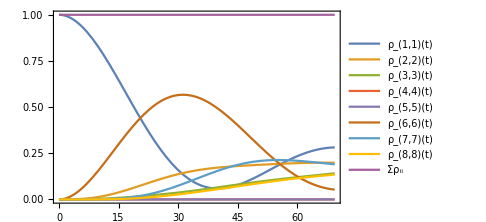

```mathematica
icEqs=Array[(rho/.t-> 0)[[#]]==rho0[[#]]&,Length[rho]];
{time,soln}= Timing[First@NDSolve[Flatten@Join[Eqs,icEqs], rho, {t,0,tmax},Method->Automatic]](*,MaxStepFraction->0.001]]*);
Print["Time to run sim: ",time];
labels=rho[[;;dim]];
AppendTo[labels,Subscript[Σρ, ii]];
lines=Re[(rho/.soln)[[;;dim]]];
AppendTo[lines,Total[(rho/.soln)[[;;dim]]]];
Plot[Evaluate[lines], {t, 0,tmax },PlotRange->All,PlotLegends->labels]
(*Plot[Evaluate[lines/.t->τ (2π)/Ωeff], {τ, 0,tmax Ωeff/(2π)},PlotRange->All,PlotLegends->labels]*)
```

## ^87 Rb - D2 line

Test the new form of eq building

```mathematica
Clear[MEqs]
MEqs[stateList_,fieldAmplitudes_,detunings_,dipoleMatrixElement_,decayRate_,dropFastOoM_,excludeIndices_]:=Module[{drop,states=stateList,Ep=fieldAmplitudes,d=dipoleMatrixElement,γ=decayRate,Δ=detunings,l=1,k=1,dim=1,dimE=1,populationRHS, coherenceRHS,populationDriving,populationDecay,coherenceDriving,coherenceDecay,RHS=0,Eqs={},HO,Ex},
(*Builds the density matrix master equation in Linblad form for each element Subscript[ρ, k,l] with k>l and k increasing in order of energy. The coherence terms are actually ρ̃=ρⅇ^-ⅈωt.

--- Params ---
fieldAmplitudes, detunings, dipoleMatrixElement, and decayRate: functions that depend on state indices j,k and field indices p to return the appropriate quantity. See usage below.

dropFastOoM: an order of magnitude of the detuning (in the chosen energy units of the states and fields, e.g. GHz).

excludeIndices: a list of indices {k,l} for which equations for Subscript[ρ, k,l] and dependence on Subscript[ρ, k,l] in other eqs will be dropped
*)
dim = Length[states];
dimE=Length[Ep];
(*--multipliers for systematically dropping terms--*)
Table[Subscript[HO, p,i,j]=DropHiOsc[Δ[p,i,j],dropFastOoM],{p,Range[dimE]},{i,Range[dim]},{j,Range[dim]}];(*for removing highly oscillatory (far off-resonant) terms*)
Table[Subscript[Ex, k,l]=Subscript[Ex, l,k]=Boole[!MemberQ[excludeIndices,{k,l}]],{l,Range[dim]},{k,Range[l,dim]}];(*for removing the equations for and terms with Subscript[ρ, k,l] if {k,l} ∈ excludeIndices*)

(*--Generate the population eqs--*)
For[k=1,k<dim+1,k++,
RHS=
-Sum[γ[j,k]Subscript[ρ, k,k][t],{j,Range[1,k-1]}]+Sum[γ[k,j]Subscript[ρ, j,j][t],{j,Range[k+1,dim]}]
-ⅈ/(2ℏ)(Sum[(-Ep[[p]]d[k,j,p]Subscript[ρ, k,j][t]*Exp[-ⅈ Δ[p,k,j]t]+Ep[[p]]*d[j,k,p]Subscript[ρ, k,j][t]Exp[ⅈ Δ[p,k,j]t])Subscript[HO, p,k,j] Subscript[Ex, k,j],{p,Range[dimE]},{j,Range[1,k-1]}]
+Sum[(Ep[[p]]d[j,k,p]Subscript[ρ, j,k][t]*Exp[-ⅈ Δ[p,j,k]t]-Ep[[p]]*d[k,j,p]Subscript[ρ, j,k][t]Exp[ⅈ Δ[p,j,k]t])Subscript[HO, p,j,k] Subscript[Ex, j,k],{p,Range[dimE]},{j,Range[k+1,dim]}]);
AppendTo[Eqs,D[Subscript[ρ, k,k][t],t]==RHS];
];
(*--Generate the coherence eqs--*)
For[l=1,l<dim+1,l++,
For[k=l+1,k<dim+1,k++,
If[!MemberQ[excludeIndices,{k,l}],
RHS=1/2(-(Sum[γ[j,k],{j,Range[1,k-1]}]+Sum[γ[j,l],{j,Range[1,l-1]}])Subscript[ρ, k,l][t]
+Sum[γ[k,j]Subscript[ρ, j,l][t](1-δ[j,l])Subscript[Ex, j,l],{j,Range[k+1,dim]}]+Sum[γ[l,j]Subscript[ρ, k,j][t](1-δ[k,j])Subscript[Ex, k,j],{j,Range[l+1,k-1]}]+Sum[γ[l,j]Subscript[ρ, j,k][t]*(1-δ[k,j])Subscript[Ex, j,k],{j,Range[k+1,dim]}]
-ⅈ/ℏ(Sum[-Ep[[p]]d[k,j,p]Subscript[ρ, l,j][t]*Exp[-ⅈ Δ[p,k,j]t] Subscript[HO, p,k,j] Subscript[Ex, l,j]+Ep[[p]]*d[j,l,p]Subscript[ρ, k,j][t]Exp[ⅈ Δ[p,l,j]t] Subscript[HO, p,l,j] Subscript[Ex, k,j],{p,Range[dimE]},{j,Range[1,l-1]}]
+Sum[Ep[[p]](d[j,l,p]Subscript[ρ, k,j][t]Exp[-ⅈ Δ[p,j,l]t] Subscript[HO, p,j,l] Subscript[Ex, k,j]-d[k,j,p]Subscript[ρ, j,l][t]Exp[-ⅈ Δ[p,k,j]t] Subscript[HO, p,k,j] Subscript[Ex, j,l]),{p,Range[dimE]},{j,Range[l,k-1]}]
+Sum[Ep[[p]]d[j,l,p]Subscript[ρ, j,k][t]*Exp[-ⅈ Δ[p,j,l]t] Subscript[HO, p,j,l] Subscript[Ex, j,k]-Ep[[p]]*d[k,j,p]Subscript[ρ, j,l][t]Exp[ⅈ Δ[p,j,k]t] Subscript[HO, p,j,k] Subscript[Ex, j,l],{p,Range[dimE]},{j,Range[k,dim]}]));
AppendTo[Eqs,D[Subscript[ρ, k,l][t],t]==RHS];
];
];
];

Eqs
]
```

```mathematica
Clear[ρ]

(*states with n,L,J,F,mF, and angular frequency (energy) in 2π*GHz wrt ground state C.o.M. energy*)

Fglist={1}(*Range[Abs[INuc-1/2],INuc+1/2]*);(*list of ground state hyperfine levels F*)
Fe1list=Fglist(*Range[Abs[INuc-1/2],INuc+1/2]*);
Fe2list={2};(*Range[Abs[INuc-3/2],INuc+3/2]*);
FivePThreeHalves=Flatten[Table[Table[{5,1,3/2,f,mf},{mf,Range[-f,f]}],{f,Fe2list}(*Range[Abs[INuc-3/2],INuc+3/2]}*)],1];
FivePOneHalf=Flatten[Table[Table[{5,1,1/2,f,mf},{mf,Range[-f,f]}],{f,Fe1list}],1];
FiveSOneHalf=Flatten[Table[Table[{5,0,1/2,f,mf},{mf,Range[-f,f]}],{f,Fglist}],1];
states=Join[FiveSOneHalf,(*FivePOneHalf,*)FivePThreeHalves];
{n,L,J,F,mF}=Transpose@states;
"Total number of states:"
dim=Length[states]

(*the energy of each state*)
ω=Table[2π Rb87fGHz[states[[i]][[;;4]]],{i,Range[dim]}];

(*lists of field amplitudes, ang. frequencies, polarization, and angle in rad*)
Clear[Ε1,Ε2,γD1,γD2,dD1,dD2](*leave symbolic so it's easy to read the equations*);

(*--define numerical constants--*)
dD1=D1MatElem;
dD2=D2MatElem;
γD1=ΓD1*10^-9;
γD2=ΓD2*10^-9;
Ε1=Ε2=0.5√(2/(c ϵ0)IsatD2SI) /GHz;

det =2π*10^-9;(*detuning. must be finite, but can be arbitrarily small... where does the 1/0 come from?*)
Efields={{Ε1,2π(Rb87fGHz[{5,1,3/2,2}]-Rb87fGHz[{5,0,1/2,1}]-det),1,0}(*,{Ε2,2π(Rb87fGHz[{5,1,3/2,2}]-Rb87fGHz[{5,0,1/2,2}])-det, 0,0}*)};
{Ep,ωp,q,θ}=Transpose@Efields;
dimE=Length[Ep];

(*--things that depend on a pair of state indices j and k--*)
E1FineReduced[j_,k_]:=Switch[Sort[{{n[[j]],L[[j]],J[[j]]},{n[[k]],L[[k]],J[[k]]}}],{{5,0,1/2},{5,1,1/2}},dD1,{{5,0,1/2},{5,1,3/2}},dD2,_,0];(*get hardcoded D1 or D2 line reduced dipole matrix element.*)

d[j_,k_,p_]:=Quiet[E1FineReduced[j,k]If[k>j,(-1)^(1-q[[p]])(-1)^(1+INuc+J[[j]]+F[[k]])√(2F[[k]]+1)SixJSymbol[{J[[k]],INuc,F[[k]]},{F[[j]],1,J[[j]]}]ClebschGordan[{F[[k]],mF[[k]]},{1,-q[[p]]},{F[[j]],mF[[j]]}],(-1)^(1+INuc+J[[j]]+F[[k]])√(2F[[k]]+1)SixJSymbol[{J[[k]],INuc,F[[k]]},{F[[j]],1,J[[j]]}]ClebschGordan[{F[[k]],mF[[k]]},{1,q[[p]]},{F[[j]],mF[[j]]}]]];(*the hyperfine dipole matrix element; the If takes care of the Hermitian conjugate. TODO: make general by including the Wigner D to allow rotations*)

γE1[j_,k_]:=Switch[Sort[{{n[[j]],L[[j]],J[[j]]},{n[[k]],L[[k]],J[[k]]}}],{{5,0,1/2},{5,1,1/2}},γD1,{{5,0,1/2},{5,1,3/2}},γD2,_,0];(*get hardcoded D1 or D2 line natural linewidth.*)

(*branching factor from an upper state k to j*)
b[{J_,F_,mF_},{JJ_,FF_,mFF_}]:=Quiet[(2F+1)SixJSymbol[{J,INuc,F},{FF,1,JJ}]^2 ClebschGordan[{F,mF},{1,mFF-mF},{FF,mFF}]^2];

(*pre-evaluate b values*)
Table[Subscript[bb, J[[j]],F[[j]],mF[[j]],J[[k]],F[[k]],mF[[k]]]=b[{J[[j]],F[[j]],mF[[j]]},{J[[k]],F[[k]],mF[[k]]}],{j,Range[dim]},{k,Range[j,dim]}];

(*decay from state k to j*)
γ[j_,k_]:=γE1[j,k](Subscript[bb, J[[j]],F[[j]],mF[[j]],J[[k]],F[[k]],mF[[k]]]/Total[Flatten[Table[Subscript[bb, J[[1]],Fg,mFg,J[[k]],F[[k]],mF[[k]]],{Fg,Fglist},{mFg,Range[-Fg,Fg]}],1]]);
(*γ[j_,k_]:=γE1[j,k](b[{J[[j]],F[[j]],mF[[j]]},{J[[k]],F[[k]],mF[[k]]}]/Total[Flatten[Table[Table[b[{J[[1]],Fg,mFg},{J[[k]],F[[k]],mF[[k]]}],{mFg,Range[-Fg,Fg]}],{Fg,Fglist}]]]);*)

Δ[p_,k_,j_]:=ωp[[p]]-(ω[[k]]-ω[[j]]);

(*pre-evaluate γ, d, and Δ values which we can "look up" by index*)
Table[γlookup[j,k]=γ[j,k],{j,Range[dim]},{k,Range[j,dim]}];
Table[dlookup[j,k,p]=d[j,k,p],{p,Range[dimE]},{j,Range[dim]},{k,Range[dim]}];
Table[Δlookup[p,k,j]=Δ[p,k,j],{p,Range[dimE]},{j,Range[dim]},{k,Range[dim]}];

(*terms with detunings of greater order of magnitude (GHz) than this will be dropped*)
drop=OoM[10]+1;(*GHz*)

(*equations to exclude for an approximate but much faster result*)
gExclude=Flatten[Table[{k,j},{j,Range[3]},{k,Range[j+1,3]}],1];(*coherences betweeen  5S1/2 hyperfine states*)
eExclude=Flatten[Table[{k,j},{j,Range[4,10]},{k,Range[j+1,10]}],1];(*coherences betweeen  5P1/2 hyperfine states*)
exclude=Join[gExclude,eExclude];

Eqs = MEqs[states,Ep,Δlookup,dlookup,γlookup,drop,exclude];(*generate the differential equations*)
"Number of equations"
Eqs//Length
"The equations to be solved:"
For[i=1,i<Length[Eqs]+1,i++,
Print[Eqs[[i]]//Expand//TraditionalForm]
]
```

Total number of states:

8

Number of equations

23

The equations to be solved:

ρ_(1,1)'(t)==(0.-0.00169173 ⅈ) ⅇ^((0.+3.95812×10^-8 ⅈ) t) Conjugate[ρ_(6,1)(t)]+(0.+0.00169173 ⅈ) ⅇ^((0.-3.95812×10^-8 ⅈ) t) ρ_(6,1)(t)+0.0381132 ρ_(4,4)(t)+0.0190566 ρ_(5,5)(t)+0.0063522 ρ_(6,6)(t)+(0.+0. ⅈ)

ρ_(2,2)'(t)==(0.-0.00293016 ⅈ) ⅇ^((0.+3.95812×10^-8 ⅈ) t) Conjugate[ρ_(7,2)(t)]+(0.+0.00293016 ⅈ) ⅇ^((0.-3.95812×10^-8 ⅈ) t) ρ_(7,2)(t)+0.0190566 ρ_(5,5)(t)+0.0254088 ρ_(6,6)(t)+0.0190566 ρ_(7,7)(t)+(0.+0. ⅈ)

ρ_(3,3)'(t)==(0.-0.00414388 ⅈ) ⅇ^((0.+3.95812×10^-8 ⅈ) t) Conjugate[ρ_(8,3)(t)]+(0.+0.00414388 ⅈ) ⅇ^((0.-3.95812×10^-8 ⅈ) t) ρ_(8,3)(t)+0.0063522 ρ_(6,6)(t)+0.0190566 ρ_(7,7)(t)+0.0381132 ρ_(8,8)(t)+(0.+0. ⅈ)

ρ_(4,4)'(t)==-0.0381132 ρ_(4,4)(t)+(0.+0. ⅈ)

ρ_(5,5)'(t)==-0.0381132 ρ_(5,5)(t)+(0.+0. ⅈ)

ρ_(6,6)'(t)==(0.+0.00169173 ⅈ) ⅇ^((0.+3.95812×10^-8 ⅈ) t) Conjugate[ρ_(6,1)(t)]-(0.+0.00169173 ⅈ) ⅇ^((0.-3.95812×10^-8 ⅈ) t) ρ_(6,1)(t)-0.0381132 ρ_(6,6)(t)+(0.+0. ⅈ)

ρ_(7,7)'(t)==(0.+0.00293016 ⅈ) ⅇ^((0.+3.95812×10^-8 ⅈ) t) Conjugate[ρ_(7,2)(t)]-(0.+0.00293016 ⅈ) ⅇ^((0.-3.95812×10^-8 ⅈ) t) ρ_(7,2)(t)-0.0381132 ρ_(7,7)(t)+(0.+0. ⅈ)

ρ_(8,8)'(t)==(0.+0.00414388 ⅈ) ⅇ^((0.+3.95812×10^-8 ⅈ) t) Conjugate[ρ_(8,3)(t)]-(0.+0.00414388 ⅈ) ⅇ^((0.-3.95812×10^-8 ⅈ) t) ρ_(8,3)(t)-0.0381132 ρ_(8,8)(t)+(0.+0. ⅈ)

ρ_(4,1)'(t)==-0.0190566 ρ_(4,1)(t)+(0.+0. ⅈ)

ρ_(5,1)'(t)==-0.0190566 ρ_(5,1)(t)+(0.+0. ⅈ)

ρ_(6,1)'(t)==(0.-0.00169173 ⅈ) ⅇ^((0.+3.95812×10^-8 ⅈ) t) Conjugate[ρ_(6,6)(t)]+(0.+0.00169173 ⅈ) ⅇ^((0.+3.95812×10^-8 ⅈ) t) ρ_(1,1)(t)-0.0190566 ρ_(6,1)(t)+(0.+0. ⅈ)

ρ_(7,1)'(t)==-0.0190566 ρ_(7,1)(t)+(0.+0. ⅈ)

ρ_(8,1)'(t)==-0.0190566 ρ_(8,1)(t)+(0.+0. ⅈ)

ρ_(4,2)'(t)==-0.0190566 ρ_(4,2)(t)+(0.+0. ⅈ)

ρ_(5,2)'(t)==-0.0190566 ρ_(5,2)(t)+(0.+0. ⅈ)

ρ_(6,2)'(t)==-0.0190566 ρ_(6,2)(t)+(0.+0. ⅈ)

ρ_(7,2)'(t)==(0.-0.00293016 ⅈ) ⅇ^((0.+3.95812×10^-8 ⅈ) t) Conjugate[ρ_(7,7)(t)]+(0.+0.00293016 ⅈ) ⅇ^((0.+3.95812×10^-8 ⅈ) t) ρ_(2,2)(t)-0.0190566 ρ_(7,2)(t)+(0.+0. ⅈ)

ρ_(8,2)'(t)==-0.0190566 ρ_(8,2)(t)+(0.+0. ⅈ)

ρ_(4,3)'(t)==-0.0190566 ρ_(4,3)(t)+(0.+0. ⅈ)

ρ_(5,3)'(t)==-0.0190566 ρ_(5,3)(t)+(0.+0. ⅈ)

ρ_(6,3)'(t)==-0.0190566 ρ_(6,3)(t)+(0.+0. ⅈ)

ρ_(7,3)'(t)==-0.0190566 ρ_(7,3)(t)+(0.+0. ⅈ)

ρ_(8,3)'(t)==(0.-0.00414388 ⅈ) ⅇ^((0.+3.95812×10^-8 ⅈ) t) Conjugate[ρ_(8,8)(t)]+(0.+0.00414388 ⅈ) ⅇ^((0.+3.95812×10^-8 ⅈ) t) ρ_(3,3)(t)-0.0190566 ρ_(8,3)(t)+(0.+0. ⅈ)

```mathematica
Subscript[Ex, 7,8]
```

Ex_(7,8)

```mathematica
Subscript[Ex, 6,4]
```

```mathematica
exclude
```

{{2,1},{3,1},{3,2},{5,4},{6,4},{7,4},{8,4},{6,5},{7,5},{8,5},{7,6},{8,6},{8,7}}

```mathematica
Table[Subscript[Ex, k,l]=Subscript[Ex, l,k]=Boole[!MemberQ[exclude,{k,l}]],{l,Range[dim]},{k,Range[l,dim]}];
```

```mathematica
MemberQ[excludeIndices,{8,7}]
```

False

```mathematica
Subscript[Ex, 8,7]
```

0

```mathematica
Subscript[Ex, 6,4]
```

1

```mathematica
(*--setup for the numerical solver--*)

(*the list of populations and coherences we're including, in the same order as in Eqs*)
rho=Join[Table[Subscript[ρ, k,k][t],{k,Range[dim]}],Complement[Flatten[Table[Subscript[ρ, k,l][t],{l,1,dim},{k,l+1,dim}],1],Array[Subscript[ρ, exclude[[#,1]],exclude[[#,2]]][t]&,Length[exclude]]]];
rho0=Array[0&,Length[rho]];
rho0[[1]]=1;
Ω1=Ε1 d[3,8,1]/ℏ;
(*Ω2=Ε2 d[8,17,2]/ℏ;*)
Ωeff=Abs[Ω1] ;
Print["Effective rabi frequency = 2π*",Ωeff GHz/10^6," MHz"]
tmax=12*2π/Ωeff;
```

Effective rabi frequency = 2π*8.28776 MHz

```mathematica
rho//Length
```

23

```mathematica
rho0//Length
```

23

```mathematica
Eqs//Length
```

23

```mathematica
icEqs=Array[(rho/.t-> 0)[[#]]==rho0[[#]]&,Length[rho]];
{time,soln}= Timing[First@NDSolve[Flatten@Join[Eqs,icEqs], rho, {t,0,tmax},Method->Automatic]](*,MaxStepFraction->0.001]]*);
Print["Time to run sim: ",time];
```

Time to run sim: 0.015625

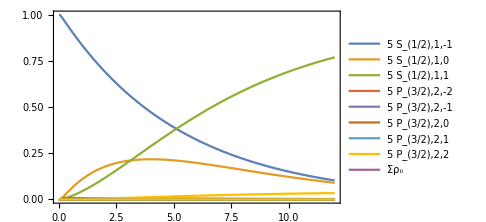

```mathematica
Plot[Evaluate[Re[rho/.soln]/.t->τ (2π)/Ωeff], {τ, 0,tmax Ωeff/(2π)},PlotRange->All,PlotLegends->labels]
```

```mathematica
exc={{1,3},{1,2}};
arr=Complement[Table[{1,j},{j,Range[5]}],exc]
```

{{1,1},{1,4},{1,5}}

```mathematica
Array[Subscript[ρ, arr[[#,1]],arr[[#,2]]]&,Length[arr]]
```

{ρ_(1,1),ρ_(1,4),ρ_(1,5)}

```mathematica
Which
```

False

```mathematica
dim
```

24

```mathematica
(dim(dim+1))/2
```

300

```mathematica
Length[Flatten[Table[{j,k},{j,Range[dim]},{k,Range[j+1,dim]}],1]]+24
```

300

```mathematica
(*equations to exclude for an approximate but much faster result*)
gExclude=Flatten[Table[{j,k},{j,Range[7]},{k,Range[j+1,8]}],1];(*coherences betweeen  5S1/2 hyperfine states*)
eExclude=Flatten[Table[{j,k},{j,Range[9,23]},{k,Range[j+1,24]}],1];(*coherences betweeen  5P3/2 hyperfine states*)
exclude=Join[gExclude,eExclude]
```

{{1,2},{1,3},{1,4},{1,5},{1,6},{1,7},{1,8},{2,3},{2,4},{2,5},{2,6},{2,7},{2,8},{3,4},{3,5},{3,6},{3,7},{3,8},{4,5},{4,6},{4,7},{4,8},{5,6},{5,7},{5,8},{6,7},{6,8},{7,8},{9,10},{9,11},{9,12},{9,13},{9,14},{9,15},{9,16},{9,17},{9,18},{9,19},{9,20},{9,21},{9,22},{9,23},{9,24},{10,11},{10,12},{10,13},{10,14},{10,15},{10,16},{10,17},{10,18},{10,19},{10,20},{10,21},{10,22},{10,23},{10,24},{11,12},{11,13},{11,14},{11,15},{11,16},{11,17},{11,18},{11,19},{11,20},{11,21},{11,22},{11,23},{11,24},{12,13},{12,14},{12,15},{12,16},{12,17},{12,18},{12,19},{12,20},{12,21},{12,22},{12,23},{12,24},{13,14},{13,15},{13,16},{13,17},{13,18},{13,19},{13,20},{13,21},{13,22},{13,23},{13,24},{14,15},{14,16},{14,17},{14,18},{14,19},{14,20},{14,21},{14,22},{14,23},{14,24},{15,16},{15,17},{15,18},{15,19},{15,20},{15,21},{15,22},{15,23},{15,24},{16,17},{16,18},{16,19},{16,20},{16,21},{16,22},{16,23},{16,24},{17,18},{17,19},{17,20},{17,21},{17,22},{17,23},{17,24},{18,19},{18,20},{18,21},{18,22},{18,23},{18,24},{19,20},{19,21},{19,22},{19,23},{19,24},{20,21},{20,22},{20,23},{20,24},{21,22},{21,23},{21,24},{22,23},{22,24},{23,24}}

{{1,2},{1,3},{1,4},{1,5},{1,6},{1,7},{1,8},{2,3},{2,4},{2,5},{2,6},{2,7},{2,8},{3,4},{3,5},{3,6},{3,7},{3,8},{4,5},{4,6},{4,7},{4,8},{5,6},{5,7},{5,8},{6,7},{6,8},{7,8},{{9,10},{9,11},{9,12},{9,13},{9,14},{9,15},{9,16},{9,17},{9,18},{9,19},{9,20},{9,21},{9,22},{9,23},{9,24},{10,11},{10,12},{10,13},{10,14},{10,15},{10,16},{10,17},{10,18},{10,19},{10,20},{10,21},{10,22},{10,23},{10,24},{11,12},{11,13},{11,14},{11,15},{11,16},{11,17},{11,18},{11,19},{11,20},{11,21},{11,22},{11,23},{11,24},{12,13},{12,14},{12,15},{12,16},{12,17},{12,18},{12,19},{12,20},{12,21},{12,22},{12,23},{12,24},{13,14},{13,15},{13,16},{13,17},{13,18},{13,19},{13,20},{13,21},{13,22},{13,23},{13,24},{14,15},{14,16},{14,17},{14,18},{14,19},{14,20},{14,21},{14,22},{14,23},{14,24},{15,16},{15,17},{15,18},{15,19},{15,20},{15,21},{15,22},{15,23},{15,24},{16,17},{16,18},{16,19},{16,20},{16,21},{16,22},{16,23},{16,24},{17,18},{17,19},{17,20},{17,21},{17,22},{17,23},{17,24},{18,19},{18,20},{18,21},{18,22},{18,23},{18,24},{19,20},{19,21},{19,22},{19,23},{19,24},{20,21},{20,22},{20,23},{20,24},{21,22},{21,23},{21,24},{22,23},{22,24},{23,24}}}

```mathematica
dim=3;
For[l=1,l<dim+1,l++,
For[k=l,k<dim+1,k++,
Print[{l,k}]
]
]
```

{1,1}

{1,2}

{1,3}

{2,2}

{2,3}

{3,3}

```mathematica
lookup=Flatten[Table[{y[l,k]=γ[l,k],Subscript[dd, l,k]=d[l,k]},{l,Range[3]},{k,Range[l,3]}],1]
```

Total::tllen: Lists of unequal length in {{1/24,bb_(1/2,1,0,1/2,1,-1),bb_(1/2,1,1,1/2,1,-1)},{bb_(1/2,2,-2,1/2,1,-1),bb_(1/2,2,-1,1/2,1,-1),bb_(1/2,2,0,1/2,1,-1),bb_(1/2,2,1,1/2,1,-1),bb_(1/2,2,2,1/2,1,-1)}} cannot be added.

Total::tllen: Lists of unequal length in {{1/24,0,bb_(1/2,1,1,1/2,1,0)},{bb_(1/2,2,-2,1/2,1,0),bb_(1/2,2,-1,1/2,1,0),bb_(1/2,2,0,1/2,1,0),bb_(1/2,2,1,1/2,1,0),bb_(1/2,2,2,1/2,1,0)}} cannot be added.

Total::tllen: Lists of unequal length in {{0,1/24,1/24},{bb_(1/2,2,-2,1/2,1,1),bb_(1/2,2,-1,1/2,1,1),bb_(1/2,2,0,1/2,1,1),bb_(1/2,2,1,1/2,1,1),bb_(1/2,2,2,1/2,1,1)}} cannot be added.

General::stop: Further output of Total::tllen will be suppressed during this calculation.

{{0,d[1,1]},{0,d[1,2]},{0,d[1,3]},{0,d[2,2]},{0,d[2,3]},{0,d[3,3]}}

```mathematica
y[1,2]
```

γ[1,2]

```mathematica
Subscript[dd, 2,3]
```

d[2,3]

```mathematica
Subscript[y, 2,3]
```

γ[2,3]

```mathematica
lookup[[3,3]]
```

Part::partw: Part 3 of {γ[3,3]} does not exist.

{{γ[1,1],γ[1,2],γ[1,3]},{γ[2,2],γ[2,3]},{γ[3,3]}}⟦3,3⟧

```mathematica
Table[γ[l,k],{l,Range[3]},{k,Range[l,3]}]
```

{{γ[1,1],γ[1,2],γ[1,3]},{γ[2,2],γ[2,3]},{γ[3,3]}}

```mathematica
ω5sOneHalfF1=2π*2.563005979089;
ω5sOneHalfF2=2π*-4.27167663181519;
ωD2=2π*384230.4844685;
ω5pThreeHalvesF0 =ωD2-2π*.3020738;
ω5pThreeHalvesF2=ωD2-2π*.072911332;
states={{5,0,1/2,1,1,ω5sOneHalfF1},{5,0,1/2,2,1,ω5sOneHalfF2},{5,0,1/2,2,2,ω5sOneHalfF2},{5,1,3/2,2,2,ω5pThreeHalvesF2}};
{n,L,J,F,mF,ω}=Transpose@states;
dim=Length[energies];
(*lists of field amplitudes, ang. frequencies, polarization, and angle in rad*)
Clear[Ε1,Ε2];
det =2π*10^-6;(*detuning. must be finite, but can be arbitrarily small... where does the 1/0 come from?*)
Efields={{Ε1,ω5pThreeHalvesF2-ω5sOneHalfF1-det,1,0}}(*,{Ε2,ω5pThreeHalvesF2-ω5sOneHalfF2-det, 0,0}}*);
{Ep,ωp,q,θ}=Transpose@Efields;
dimE=Length[Ep];
(*things that depend on a pair of state indices j and k:*)
E1FineReduced[j_,k_]:=Switch[Sort[{{n[[j]],L[[j]],J[[j]]},{n[[k]],L[[k]],J[[k]]}}],{{5,0,1/2},{5,1,1/2}},D1,{{5,0,1/2},{5,1,3/2}},D2,_,0];
Δ[p_,k_,j_]:=ωp[[p]]-(ω[[k]]-ω[[j]])
```

see which transitions are dropped using my DropHiOsc function

```mathematica
OoM[x_]:=Floor[Log10[Abs[x]]0.5]+1;
```

```mathematica
oom=OoM[2π 6.8]+1;(*in GHz*)
For[i=1,i<dimE+1,i++,
For[k=1,k<Length[states]+1,k++,
For[j=1,j<k,j++,
msg=If[DropHiOsc[Δ[i,k,j],oom]==0,"too far detuned - drop!  ","keep.  "];
If[k!=j,Print[msg,KetFormat[states[[k]]],"↔",KetFormat[states[[j]]]," Δ=2π*",Δ[i,k,j]/(2π),"GHz, field ",i,"; {k,j}=",{k,j}]]
]
]
]
```

too far detuned - drop!  5 S_(1/2),2,1↔5 S_(1/2),1,1 Δ=2π*384235.GHz, field 1; {k,j}={2,1}

too far detuned - drop!  5 S_(1/2),2,2↔5 S_(1/2),1,1 Δ=2π*384235.GHz, field 1; {k,j}={3,1}

too far detuned - drop!  5 S_(1/2),2,2↔5 S_(1/2),2,1 Δ=2π*384228.GHz, field 1; {k,j}={3,2}

keep.  5 P_(3/2),2,2↔5 S_(1/2),1,1 Δ=2π*-9.99997×10^-7GHz, field 1; {k,j}={4,1}

keep.  5 P_(3/2),2,2↔5 S_(1/2),2,1 Δ=2π*-6.83468GHz, field 1; {k,j}={4,2}

keep.  5 P_(3/2),2,2↔5 S_(1/2),2,2 Δ=2π*-6.83468GHz, field 1; {k,j}={4,3}

```mathematica
OoM[6.834683610947995]
```

1

```mathematica
OoM[x_]:=Floor[Log10[Abs[x]]0.5]+1;
OrbAngLetter[L_]:=Switch[L,0,"S",1,"P",2,"D",3,"F"];
KetFormat[state_]:=state[[1]] Subscript[OrbAngLetter[state[[2]]], state[[3]]//Rationalize],state[[4]],state[[5]];(*assumes list state with {n,L,J,F,mF,...}*)
```

```mathematica
Floor[Log[10,10]+0.5]
```

1

```mathematica
s=states[[2]];
s[[1]]
OrbAngLetter[s[[2]]]
s[[3]]//Rationalize
s[[4]]
s[[5]]
```

5

S

1/2

2

1

```mathematica
states[[2]][[1]]
```

5

```mathematica
3/2//Rationalize
```

3/2

```mathematica
If[1,"yay!"]
```

If[1,yay!]

```mathematica
BooleanQ
```

```mathematica
Do[Print[J[[i]]],{i,Range[Length[states]]}]
```

1/2

1/2

1/2

3/2

```mathematica
{n[[j]],L[[j]],J[[j]]}/.j->4
```

Part::pkspec1: The expression j cannot be used as a part specification.

General::stop: Further output of Part::pkspec1 will be suppressed during this calculation.

{5,1,3/2}

```mathematica
Sort[{{n[[j]],L[[j]],J[[j]]}/.j->4,{n[[j]],L[[j]],J[[j]]}/.j->1}]
```

Part::pkspec1: The expression j cannot be used as a part specification.

General::stop: Further output of Part::pkspec1 will be suppressed during this calculation.

{{5,0,1/2},{5,1,3/2}}

```mathematica
d[j_,k_,p_]:=Quiet[Boole[Abs[L[[j]]-L[[k]]]==1] E1FineReduced[j,k]If[k>j,(-1)^(1-q[[p]])(-1)^(1+INuc+J[[j]]+F[[k]])√(2F[[k]]+1)SixJSymbol[{J[[k]],INuc,F[[k]]},{F[[j]],1,J[[j]]}]ClebschGordan[{F[[k]],mF[[k]]},{1,-q[[p]]},{F[[j]],mF[[j]]}],(-1)^(1+INuc+J[[j]]+F[[k]])√(2F[[k]]+1)SixJSymbol[{J[[k]],INuc,F[[k]]},{F[[j]],1,J[[j]]}]ClebschGordan[{F[[k]],mF[[k]]},{1,q[[p]]},{F[[j]],mF[[j]]}]]];
```

```mathematica
k=4;j=1;p=1;
"k=4,j=1"
(-1)^(1-q[[p]])(-1)^(1+INuc+J[[j]]+F[[k]])√(2F[[k]]+1)SixJSymbol[{J[[k]],INuc,F[[k]]},{F[[j]],1,J[[j]]}]ClebschGordan[{F[[k]],mF[[k]]},{1,-q[[p]]},{F[[j]],mF[[j]]}]
(-1)^(1+INuc+J[[j]]+F[[k]])√(2F[[k]]+1)SixJSymbol[{J[[k]],INuc,F[[k]]},{F[[j]],1,J[[j]]}]ClebschGordan[{F[[k]],mF[[k]]},{1,q[[p]]},{F[[j]],mF[[j]]}]
"k=1,j=4"
k=1;j=4;
(-1)^(1-q[[p]])(-1)^(1+INuc+J[[j]]+F[[k]])√(2F[[k]]+1)SixJSymbol[{J[[k]],INuc,F[[k]]},{F[[j]],1,J[[j]]}]ClebschGordan[{F[[k]],mF[[k]]},{1,-q[[p]]},{F[[j]],mF[[j]]}]
(-1)^(1+INuc+J[[j]]+F[[k]])√(2F[[k]]+1)SixJSymbol[{J[[k]],INuc,F[[k]]},{F[[j]],1,J[[j]]}]ClebschGordan[{F[[k]],mF[[k]]},{1,q[[p]]},{F[[j]],mF[[j]]}]
```

k=4,j=1

1/(2 √2)

ClebschGordan::phy: ThreeJSymbol[{2,2},{1,1},{1,-1}] is not physical.

0

k=1,j=4

ClebschGordan::phy: ThreeJSymbol[{1,1},{1,-1},{2,-2}] is not physical.

0

1/(2 √2)

```mathematica
Switch[{{5,0,1/2},{5,1,3/2}},{{5,0,1/2},{5,1,1/2}},D1,{{5,0,1/2},{5,1,3/2}},D2,_,0]
```

D2

```mathematica
E1FineReduced[1,4]
```

0

```mathematica
Do[Print[Boole[Abs[L[[i]]-L[[j]]]==1] E1FineReduced[i,j], "  transition:",states[[i]],"->",states[[j]]],{i,Range[Length[states]]},{j,Range[Length[states]]}]
```

0  transition:{5,0,1/2,1,1,16.1038}->{5,0,1/2,1,1,16.1038}

0  transition:{5,0,1/2,1,1,16.1038}->{5,0,1/2,2,1,-26.8397}

0  transition:{5,0,1/2,1,1,16.1038}->{5,0,1/2,2,2,-26.8397}

D2  transition:{5,0,1/2,1,1,16.1038}->{5,1,3/2,2,2,2.41419×10^6}

0  transition:{5,0,1/2,2,1,-26.8397}->{5,0,1/2,1,1,16.1038}

0  transition:{5,0,1/2,2,1,-26.8397}->{5,0,1/2,2,1,-26.8397}

0  transition:{5,0,1/2,2,1,-26.8397}->{5,0,1/2,2,2,-26.8397}

D2  transition:{5,0,1/2,2,1,-26.8397}->{5,1,3/2,2,2,2.41419×10^6}

0  transition:{5,0,1/2,2,2,-26.8397}->{5,0,1/2,1,1,16.1038}

0  transition:{5,0,1/2,2,2,-26.8397}->{5,0,1/2,2,1,-26.8397}

0  transition:{5,0,1/2,2,2,-26.8397}->{5,0,1/2,2,2,-26.8397}

D2  transition:{5,0,1/2,2,2,-26.8397}->{5,1,3/2,2,2,2.41419×10^6}

D2  transition:{5,1,3/2,2,2,2.41419×10^6}->{5,0,1/2,1,1,16.1038}

D2  transition:{5,1,3/2,2,2,2.41419×10^6}->{5,0,1/2,2,1,-26.8397}

D2  transition:{5,1,3/2,2,2,2.41419×10^6}->{5,0,1/2,2,2,-26.8397}

0  transition:{5,1,3/2,2,2,2.41419×10^6}->{5,1,3/2,2,2,2.41419×10^6}

```mathematica
ρ=({{ρgg, ρge}, {ρeg, ρee}});
ee=({{0}, {1}});
gg=({{1}, {0}});
σeg=Dot[ee,Transpose[gg]];(*raising op*)
σge=Dot[gg,Transpose[ee]];(*lowering op*)
γ/2(σeg σge ρ+ρ σeg σge -2σge ρ σeg)
```

{{0,0},{0,0}}

```mathematica
Dot[ee,Transpose[gg]]//MatrixForm
```

(0 | 0
1 | 0)

```mathematica
σeg σge
```

{{0,0},{0,0}}

```mathematica
.gg
```

{{0},{1}}

```mathematica
ΓD2/(2π)/10^9
```

0.0060659

```mathematica
E1FineReduced[j_,k_]:=Switch[Sort[{{n[[j]],L[[j]],J[[j]]},{n[[k]],L[[k]],J[[k]]}}],{{5,0,1/2},{5,1,1/2}},D1,{{5,0,1/2},{5,1,3/2}},D2,_,0];
states={{5,0,1/2},{5,1,1/2},{5,1,3/2}};
{n,L,J}=Transpose@states;
E1FineReduced[1,1]
E1FineReduced[1,2]
E1FineReduced[2,3]
E1FineReduced[1,3]
```

0

D1

0

D2

```mathematica
FivePThreeHalves=Flatten[Table[Table[{5,1,3/2,f,mf},{mf,Range[-f,f]}],{f,Range[Abs[INuc-3/2],INuc+3/2]}],1]
%//Length
FivePOneHalf=Flatten[Table[Table[{5,1,1/2,f,mf},{mf,Range[-f,f]}],{f,Range[Abs[INuc-1/2],INuc+1/2]}],1]
%//Length
FiveSOneHalf=Flatten[Table[Table[{5,0,1/2,f,mf},{mf,Range[-f,f]}],{f,Range[Abs[INuc-1/2],INuc+1/2]}],1]
%//Length
states=Join[FiveSOneHalf,FivePOneHalf,FivePThreeHalves]
%//Length
```

{{5,1,3/2,0,0},{5,1,3/2,1,-1},{5,1,3/2,1,0},{5,1,3/2,1,1},{5,1,3/2,2,-2},{5,1,3/2,2,-1},{5,1,3/2,2,0},{5,1,3/2,2,1},{5,1,3/2,2,2},{5,1,3/2,3,-3},{5,1,3/2,3,-2},{5,1,3/2,3,-1},{5,1,3/2,3,0},{5,1,3/2,3,1},{5,1,3/2,3,2},{5,1,3/2,3,3}}

16

{{5,1,1/2,1,-1},{5,1,1/2,1,0},{5,1,1/2,1,1},{5,1,1/2,2,-2},{5,1,1/2,2,-1},{5,1,1/2,2,0},{5,1,1/2,2,1},{5,1,1/2,2,2}}

8

{{5,0,1/2,1,-1},{5,0,1/2,1,0},{5,0,1/2,1,1},{5,0,1/2,2,-2},{5,0,1/2,2,-1},{5,0,1/2,2,0},{5,0,1/2,2,1},{5,0,1/2,2,2}}

8

{{5,0,1/2,1,-1},{5,0,1/2,1,0},{5,0,1/2,1,1},{5,0,1/2,2,-2},{5,0,1/2,2,-1},{5,0,1/2,2,0},{5,0,1/2,2,1},{5,0,1/2,2,2},{5,1,1/2,1,-1},{5,1,1/2,1,0},{5,1,1/2,1,1},{5,1,1/2,2,-2},{5,1,1/2,2,-1},{5,1,1/2,2,0},{5,1,1/2,2,1},{5,1,1/2,2,2},{5,1,3/2,0,0},{5,1,3/2,1,-1},{5,1,3/2,1,0},{5,1,3/2,1,1},{5,1,3/2,2,-2},{5,1,3/2,2,-1},{5,1,3/2,2,0},{5,1,3/2,2,1},{5,1,3/2,2,2},{5,1,3/2,3,-3},{5,1,3/2,3,-2},{5,1,3/2,3,-1},{5,1,3/2,3,0},{5,1,3/2,3,1},{5,1,3/2,3,2},{5,1,3/2,3,3}}

32